# BH to WH Transition

## One way wormhole : a=r_H ( =1 ?)

```mathematica
Quit[];
```

```mathematica
Clear["Global`*"];
```

## Metric, V_eff, Horizon definitions

```mathematica
(*metric*) 
F[x_]:=SetPrecision[(3 -(8 mass[leta,a])/x+x^2/(3 leta^2)+leta/x ArcTan[x/leta]),20];
(*I dont include the minus sign on the gtt definition *)
gtt[x_]:=SetPrecision[ 1/4 F[√(x^2+a^2)],20];
grr[x_]:= SetPrecision[((x^2+a^2+2 leta^2)^2)/((x^2+a^2+leta^2)^2 F[√(x^2+a^2)]),20];
(**)
gθθ[x_]:=SetPrecision[x^2+a^2,20];
p[x_]:=SetPrecision[ √gθθ[x],20];
PsiSquare[x_]:=SetPrecision[-ε/(8 π leta^2)*(x^2 grr[x])/(x^2+leta^2),20];
(*useful definitions (for "easier" calculations) *)
(*h[x_]:=SetPrecision[√(gtt[x]/grr[x]),20];*)
(* η=-leta^2/ε;*)

(*potential*)
Veff[x_,lam_]:= Evaluate[SetPrecision[gtt[x]/p[x]^2 lam(lam+1)+1/(2 grr[x]^2 p[x])( 2 gtt[x] grr [x] D[p[x],{x,2}]+grr[x]  D[gtt[x],x]  D[p[x],x] -gtt[x] D[grr[x],x]   D[p[x],x] )  ,100]] ;
```

```mathematica
(*
Use if you want  Subscript[r, H] = 1  always 
*)
mass[leta_,a_]:=mass[leta,a]=(√(1+a^2) (1+a^2+9 leta^2))/(24 leta^2)+1/8 leta ArcTan[(√(1+a^2))/leta];
```

```mathematica
horizonsol[letain_,ain_]:=
NumberForm[NSolve[3 -(8 mass[leta,a])/(√(r^2+a^2))+(r^2+a^2)/(3 leta^2)+leta/(√(r^2+a^2))ArcTan[(√(r^2+a^2))/leta]==0/.leta->letain/.a->ain,r,Reals],200][[1,2,1,2]]
```

```mathematica
horizonsol[#,1]&/@{1,2,5,10}
horizonsol[1,#]&/@{1,2,5,10}
```

{1.,1.,1.,1.}

{1.,1.,1.,1.}

```mathematica
mass[#,1]&/@{0.8,2,5,10,100}//N
```

{0.820072,0.713663,0.707321,0.707121,0.707107}

```mathematica
(*  testing a new approach/idea  *)
(* horizontest[letain_,ain_]:= *)
(* we want a = Subscript[r, H] hence, a is the value of r that solves the equation for the event horizon *)
horizontest[letain_,min_]:= NumberForm[NSolve[3 -(8 m)/(√(r^2+a^2))+(r^2+a^2)/(3 leta^2)+leta/(√(r^2+a^2))ArcTan[(√(r^2+a^2))/leta]==0/.leta->letain/.m->min/.a->r,r,Reals],200][[1,2,1,2]]
```

```mathematica
horizontest[1,#]&/@{1,2,3}
horizontest[#,1]&/@{1,2,3}
```

{1.22753,1.91751,2.37559}

{1.22753,1.37674,1.4039}

## Plot Functions

## plotfunc functions (for a & leta) + ploshowfunc definitions

----------  DOCUMENTATION  -----------

plotalphafunc : Takes 3 arguments ( value, List[3elements], value ). Provide leta value,  a List with 3 values 				for alpha , & a value for lambda.  The function will define 3 plots (with fixed legend 					positions) named V1,V2,V3 for the 3  different  values of alpha. The legend display values are 				automatically updated

                     ------------------------------------------------------------------------------------------
                     
 plotshowfunc :Takes 2 (list) arguments ( { horiz_range }, { vertical_range }) .Provide the 								range({horizontal},{vertical} ) takes automatically the 3 plots defined by the  							“plotalphafunc” function and shows them together in a single image. 
           
                      ------------------------------------------------------------------------------------------
                      
 plotletafunc : (almost identical with plotalphafunc) Takes 3 arguments ( value, List[3elements], value ). 				Provide alpha value,  a List with 3 values for leta , & a value for lambda.  The function will 				define 3 plots (with fixed legend positions) named V1,V2,V3 for the 3  different  values of 					alpha. The legend display values are automatically updated
 
 --------------------------------------------

```mathematica
(*  
StringTemplate["α = ``"][alist3values[[1]]]  *)
```

```mathematica
plotalphafunc[letain_,alist3values_,lambdain_]:=Block[{ε=1,leta=letain},
times=50;
(**)
Block[{a=alist3values[[1]]},
 V1=Plot[{Veff[r,lambdain]},{r,-10*leta,10*leta},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["α = ``"][alist3values[[1]]],15]},{0.71,0.8}]},PlotStyle->colorlist[[1]],Frame->True];
];
(**)
Block[{a=alist3values[[2]]},
 V2=Plot[{Veff[r,lambdain]},{r,-10*leta,10*leta},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["α = ``"][alist3values[[2]]],15]},{0.71,0.7}]},PlotStyle->colorlist[[2]],Frame->True];
];
(**)
Block[{a=alist3values[[3]]},
 V3=Plot[{Veff[r,lambdain]},{r,-10*leta,10*leta},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["α = ``"][alist3values[[3]]],15]},{0.71,0.6}]},PlotStyle->colorlist[[3]],Frame->True];
];
];
```

Example

```mathematica
plotalphafunc[5,List[0.2,0.4,0.9],0]
```

```mathematica
plotshowfunc[horizontalrange_,verticalrange_]:=Show[{V1,V2,V3},PlotRange->{horizontalrange,verticalrange}(*{{1,10},{0,0.12}}*),ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

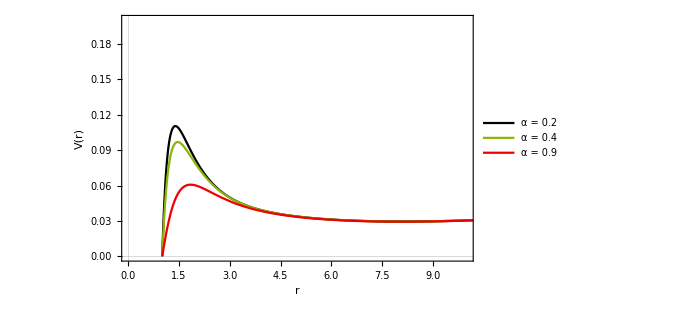

```mathematica
plotshowfunc[{0,10},{0,0.2}]
```

```mathematica
plotletafunc[ain_,letalist3values_,lambdain_,horpos_,vertpos_]:=Block[{ε=1,a=ain},
times=50;
(**)
Block[{leta=letalist3values[[1]]},
 V1=Plot[{Veff[r,lambdain]},{r,-10*leta,10*leta},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["ℓ_η = ``"][letalist3values[[1]]],15]},{0.71,0.8}]},PlotStyle->colorlist[[1]],Frame->True];
];
(**)
Block[{leta=letalist3values[[2]]},
 V2=Plot[{Veff[r,lambdain]},{r,-10*leta,10*leta},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["ℓ_η = ``"][letalist3values[[2]]],15]},{0.71,0.7}]},PlotStyle->colorlist[[2]],Frame->True];
];
(**)
Block[{leta=letalist3values[[3]]},
 V3=Plot[{Veff[r,lambdain]},{r,-10*leta,10*leta},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[(*"ℓ_η=0.5"*)StringTemplate["ℓ_η = ``"][letalist3values[[3]]],15]},{0.71,0.6}]},PlotStyle->colorlist[[3]],Frame->True];
];
];
```

Example

```mathematica
plotletafunc[0.5,{3,5,10},0]
```

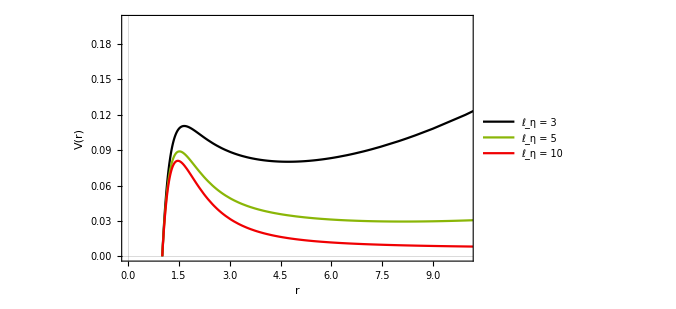

```mathematica
plotshowfunc[{0,10},{0,0.2}]
```

```mathematica
Options[PlotLegends]
```

{}

## Colors for plots

```mathematica
CD3 = ColorData[3,"ColorList"];
colorlist= CD3[[#]]& /@{1,4,6,3};
newred=ColorData[16,"ColorList"][[9]];
colorlist =  Insert[colorlist,newred,3]//Append[ColorData[14,"ColorList"][[2]]]
```

{RGBColor[0., 0., 0.],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.9411764705882353, 0., 0.00784313725490196],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744]}

```mathematica
{RGBColor[0., 0., 0.],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.9411764705882353, 0., 0.00784313725490196],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882]}
```

```mathematica
ColorData[#,"ColorList"]& /@ Range[13,20]
```

{{RGBColor[0.6588235294117647, 0.4980392156862745, 0.49019607843137253],RGBColor[0.7215686274509804, 0.1843137254901961, 0.050980392156862744],RGBColor[0.803921568627451, 0.5450980392156862, 0.4588235294117647],RGBColor[0.8156862745098039, 0.6901960784313725, 0.6313725490196078],RGBColor[0.9490196078431372, 0.8745098039215686, 0.7176470588235294],RGBColor[0.3803921568627451, 0.3843137254901961, 0.6352941176470588],RGBColor[0.23137254901960785, 0.20784313725490197, 0.5529411764705883],RGBColor[0.5843137254901961, 0.5607843137254902, 0.6627450980392157],RGBColor[0.4666666666666667, 0.27450980392156865, 0.34901960784313724],RGBColor[0.596078431372549, 0.27450980392156865, 0.36470588235294116]},{RGBColor[0.8352941176470589, 0.5764705882352941, 0.5607843137254902],RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744],RGBColor[1., 0.7333333333333333, 0.2],RGBColor[0.996078431372549, 0.9490196078431372, 0.44313725490196076],RGBColor[0.7058823529411765, 0.6862745098039216, 0.30196078431372547],RGBColor[0.41568627450980394, 0.5450980392156862, 0.12156862745098039],RGBColor[0.0196078431372549, 0.20784313725490197, 0.4627450980392157],RGBColor[0.6862745098039216, 0.7215686274509804, 0.8117647058823529],RGBColor[0.42745098039215684, 0.06666666666666667, 0.1568627450980392],RGBColor[0.8549019607843137, 0.19607843137254902, 0.27450980392156865]},{RGBColor[0.40784313725490196, 0.15294117647058825, 0.13725490196078433],RGBColor[0.6588235294117647, 0.5607843137254902, 0.5333333333333333],RGBColor[0.8313725490196079, 0.43529411764705883, 0.12941176470588237],RGBColor[0.8941176470588236, 0.8274509803921568, 0.7647058823529411],RGBColor[0.9372549019607843, 0.7764705882352941, 0.3137254901960784],RGBColor[0.23921568627450981, 0.27058823529411763, 0.4627450980392157],RGBColor[0.23529411764705882, 0.1450980392156863, 0.4588235294117647],RGBColor[0.36470588235294116, 0.23921568627450981, 0.43137254901960786],RGBColor[0.2196078431372549, 0.12549019607843137, 0.18823529411764706],RGBColor[0.5529411764705883, 0.12941176470588237, 0.2235294117647059],RGBColor[0.7058823529411765, 0.2627450980392157, 0.27058823529411763]},{RGBColor[0.4549019607843137, 0.050980392156862744, 0.023529411764705882],RGBColor[0.6784313725490196, 0.3137254901960784, 0.],RGBColor[0.9058823529411765, 0.6392156862745098, 0.07058823529411765],RGBColor[0.16470588235294117, 0.41568627450980394, 0.11764705882352941],RGBColor[0.8549019607843137, 0.9607843137254902, 1.],RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333],RGBColor[0.6392156862745098, 0.5607843137254902, 0.7529411764705882],RGBColor[0.1450980392156863, 0.11372549019607843, 0.16470588235294117],RGBColor[0.9411764705882353, 0., 0.00784313725490196]},{RGBColor[0.2823529411764706, 0.22745098039215686, 0.2235294117647059],RGBColor[0.5647058823529412, 0.23137254901960785, 0.15294117647058825],RGBColor[0.6392156862745098, 0.39215686274509803, 0.3333333333333333],RGBColor[0.8627450980392157, 0.6196078431372549, 0.2627450980392157],RGBColor[0.9647058823529412, 0.788235294117647, 0.5254901960784314],RGBColor[0.4588235294117647, 0.592156862745098, 0.4627450980392157],RGBColor[0.23921568627450981, 0.45098039215686275, 0.24705882352941178],RGBColor[0.34509803921568627, 0.5803921568627451, 0.6901960784313725],RGBColor[0.1843137254901961, 0.39215686274509803, 0.49019607843137253],RGBColor[0.5686274509803921, 0.7490196078431373, 0.8431372549019608]},{RGBColor[0.7647058823529411, 0.5568627450980392, 0.5411764705882353],RGBColor[0.9921568627450981, 0.788235294117647, 0.7568627450980392],RGBColor[0.29411764705882354, 0.19215686274509805, 0.10588235294117647],RGBColor[0.37254901960784315, 0.2784313725490196, 0.19215686274509805],RGBColor[0.29411764705882354, 0.27058823529411763, 0.18823529411764706],RGBColor[0.7098039215686275, 0.6980392156862745, 0.5058823529411764],RGBColor[0.8705882352941177, 0.8784313725490196, 0.6901960784313725],RGBColor[0.27058823529411763, 0.33725490196078434, 0.28627450980392155],RGBColor[0.6980392156862745, 0.43529411764705883, 0.4470588235294118]},{RGBColor[0.5686274509803921, 0.043137254901960784, 0.],RGBColor[0.5607843137254902, 0.22745098039215686, 0.2],RGBColor[0.6627450980392157, 0.3333333333333333, 0.],RGBColor[0.8470588235294118, 0.6392156862745098, 0.42745098039215684],RGBColor[0.7686274509803922, 0.4627450980392157, 0.14901960784313725],RGBColor[0.01568627450980392, 0.19215686274509805, 0.09803921568627451],RGBColor[0.19215686274509805, 0.3686274509803922, 0.27450980392156865],RGBColor[0.4, 0.5254901960784314, 0.4588235294117647],RGBColor[0.06666666666666667, 0.15294117647058825, 0.20784313725490197]},{RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098],RGBColor[0.9019607843137255, 0.19607843137254902, 0.12941176470588237],RGBColor[0.3568627450980392, 0.054901960784313725, 0.01568627450980392],RGBColor[0.6823529411764706, 0.41568627450980394, 0.],RGBColor[0.8352941176470589, 0.6274509803921569, 0.08627450980392157],RGBColor[0.9803921568627451, 0.7803921568627451, 0.25882352941176473],RGBColor[1., 0.9058823529411765, 0.6549019607843137],RGBColor[0.3843137254901961, 0.6, 0.8784313725490196],RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784],RGBColor[0.12549019607843137, 0.36470588235294116, 0.6784313725490196]}}

## Analysis & FD Code Setup

## tortoise

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
leta=0.8;a=1;ε=1;
(**)
Print["Horizon = ",horizonsol[leta,a]]
x= First[x1/. NDSolve[{x1'[xstar]==((1/4(3 -(8 mass[leta,a])/(√(x1[xstar]^2+a^2))+(x1[xstar]^2+a^2)/(3 leta^2)+leta/(√(x1[xstar]^2+a^2))ArcTan[(√(x1[xstar]^2+a^2))/leta]))/(((x1[xstar]^2+a^2+2 leta^2)^2)/((x1[xstar]^2+a^2+leta^2)^2)(1/(3 -(8 mass[leta,a])/(√(x1[xstar]^2+a^2))+(x1[xstar]^2+a^2)/(3 leta^2)+leta/(√(x1[xstar]^2+a^2))ArcTan[(√(x1[xstar]^2+a^2))/leta]))) )^(1/2),x1[0]==SetPrecision[1.01*horizonsol[leta,a],200](*SetPrecision[1.01*horizonsol[leta,a],200]*)(*throat @ x=0SetPrecision[1.01*horizonsol[leta,a],200]*)},
x1,{xstar,-10000,10000},Method->Automatic,
MaxSteps->10^7,
WorkingPrecision->100,
AccuracyGoal->50,
PrecisionGoal->20,
InterpolationOrder->All]]
{xstarmin,xstarmax}=InterpolatingFunctionDomain[x][[1]]
x[#]& /@{xstarmin,xstarmax}
```

Horizon = 1.

NDSolve::precw: The precision of the differential equation ({{x1'[xstar]==1/2 √((Plus[«2»]^2 Plus[«4»]^2)/Plus[«2»]^2),x1[0]==1.010000000000000230926389122032560408115386962890625},{},{},{},{}}) is less than WorkingPrecision (100.).

NDSolve::ndsz: At xstar == 5.138115026923115205595567832759217975677650359482432028964889117397195804364436136867693697679365263, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[{{-10000.00000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000, 5.138115026923115205595567832759217975677650359482432028964889117397195804364436136867693697679365263}}, <>]

{-10000.,5.138115026923115205595567832759217975677650359482432028964889117397195804364436136867693697679365263}

{1.000000000000000237820918792115873133761648692591701028502106712873979370426428684861307514835312,2.×10^87}

## Further checking r_*vs V_eff

### General

Now we just check the general behavior of the r(r_*) function and how it may affect the V_eff

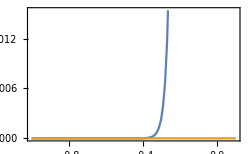

```mathematica
Plot[{x[xstar],horizonsol[leta,a]},{xstar,-1,0.1},PlotRange->Automatic,ImageSize->250,Frame->True]
```

Horizon = 1.

a = 1

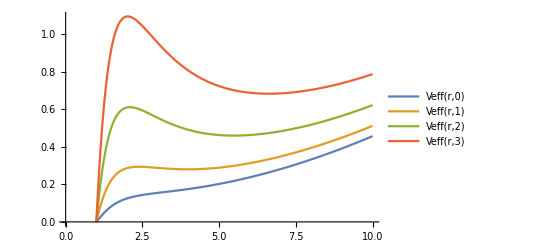
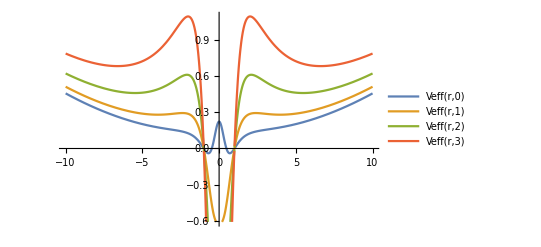

```mathematica
Block[{leta=2,a=1,ε=1 },
Print["Horizon = ",horizonsol[leta,a]];
Print["a = ",a];
VrPlot=Plot[{Veff[r,0],Veff[r,1],Veff[r,2],Veff[r,3]},{r,horizonsol[leta,a],10},PlotRange->Automatic(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
VrPlot2=Plot[{Veff[r,0],Veff[r,1],Veff[r,2],Veff[r,3]},{r,-10,10},PlotRange->Automatic(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
Show[VrPlot]
Show[VrPlot2]
]
```

### Plots !

lambda plot

```mathematica
plotl[letain_,ain_,lamlist_,horpos_,verpos_]:=
Block[{leta=letain,a=ain},
Print["Horizon = ",horizonsol[leta,a]];
legendstyle={Style[StringTemplate["ℓ = ``"][lamlist[[1]]],15],Style[StringTemplate["ℓ = ``"][lamlist[[2]]],15],Style[StringTemplate["ℓ = ``"][lamlist[[3]]],15]};
VstarPlot=Plot[{Veff[r,lamlist[[1]]],Veff[r,lamlist[[2]]],Veff[r,lamlist[[3]]]},{r,horizonsol[leta,a],100},PlotRange->All,PlotTheme->"Scientific" ,PlotStyle->colorlist ,PlotLegends->{ Placed[legendstyle,{horpos,verpos}]},
ImageSize->500];
]
```

Mass plots ?

```mathematica
Plot3D[mass[leta,a],{leta,0,10},{a,0,5},AxesLabel->{"leta" ,"α"}]
```

-Graphics3D-

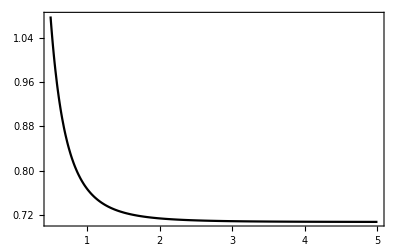

```mathematica
Plot[mass[leta,1],{leta,0.5,5},PlotRange->All,PlotTheme->"Scientific",PlotStyle->colorlist[[1]],Frame->True,FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

## Finite Difference Code

### FD - Code

Finite Difference - Implementation CODE

```mathematica
FDrin[start_,stop_,iter_,tfinal_,lam_]:=(
Clear[ψ,Length1,Δrstar,Δt,imax,imin,lambda,Adis,Bdis,jmax,σ,center,ψinit2,ψinit,V,ψinit3,ψbound,ψbound2];

(*Discretization setup*)
(*rstarmax=stop; rstarmin=start;*) Length1=stop-start;
 Δrstar=Length1/iter; Δt=Δrstar*0.7;
imax=IntegerPart[N[stop/Δrstar]];imin=IntegerPart[N[start/Δrstar]];
jmax = IntegerPart[N[tfinal/Δt]];
(**)
lambda=lam;
(*-------messages to check code behavior-------*)
printstyle={Blue,14,Italic,FontFamily->"Courier"};
Print["leta = ",leta,", m = ",N[mass[leta,a]] , ", lambda = ",lambda];
Print["r_horizon = ",horizonsol[leta,a]];
Print[Style["Location of Gaussian's center = ",Blue,14,Italic,FontFamily->"Courier"],Style[x[0],Blue,14,Italic,FontFamily->"Courier"]];
(**)
Print[Style["# of Iterations in space = ",printstyle],Style[iter,14,Blue,Italic]];
(**)
Print[ Style["(r_*)^max =  ",printstyle],Style[stop " , ",printstyle],
Style["r^max =  ",printstyle], Style[NumberForm[ x[stop],20],printstyle]];
Print[ Style["(r_*)^min =  ",printstyle],Style[start " , ",printstyle],
Style[" r^min =  ",printstyle], Style[NumberForm[ x[start],20],printstyle]];
(**)
Print[Style[ "I_max = ",printstyle],Style[imax,printstyle]];
Print[Style[ "I_min = ",printstyle],Style[imin,printstyle]];
(**)
Print[Style["Space Discretization step = ",printstyle],Style[N[Δrstar],printstyle]];
Print[Style["t_final/M = ",printstyle],Style[N[tfinal/N[mass[leta,a]]],printstyle]];
Print[Style[ "# of Iterations in time = J_max = ",printstyle],Style[jmax,printstyle]];
Print[Style["Time Discretization step = ",printstyle],Style[Δt,printstyle]];
Print[Style["Δt/(Δr_*) = ",printstyle],Style[N[Δt/Δrstar],printstyle]];(*--V effective & functions A(r)/B(r)Discretization--*)
(*Do[V[i]=Veff[r[i*Δrstar],lam],{i,imin,imax}];
Do[Adis[i]=A[r[i*Δrstar]],{i,imin,imax}];
Do[Bdis[i]=B[r[i*Δrstar]],{i,imin,imax}];*)
(*interVeff=Interpolation[Table[{rstar,Veff[r[rstar],lam]},{rstar,-1000,rstarmax,0.1}],InterpolationOrder->3];*)

V[i_]:=V[i]=(*interVeff[i*Δrstar]*)SetPrecision[ Veff[x[i*Δrstar],lam],100];

(*--------Initial Condtions--------*) 
σ=0.1;center=0;
ψ[i_,0]:=ψinit2[rstar] /.rstar->i Δrstar  ;
ψinit2[rstar_]:=SetPrecision[1/10 Exp[-(rstar-center)^2/(2 σ^2)],100];
ψ[i_,-1]:=ψinit[x[rstar]]  /.rstar->i Δrstar ;
ψinit[x[rstar_]]=0; 
(*-------Boundary Condition(s)-------*)
ψ[imax,j_]:=ψ[imax,j]= 0;
(*ψ[imin,j_]:=ψ[imin,j]= 0;*)(*comment out when ther is a horizon*)
(*--------Iterating Scheme---------*)

(*SetPrecision[ψ[imax-1,j-1]+(((Adis[imax-1] Bdis[imax-1]+Adis[imax] Bdis[imax])/2 Δt-Δrstar)/((Adis[imax-1] Bdis[imax-1]+Adis[imax] Bdis[imax])/2 Δt+Δrstar))*( ψ[imax-1,j]-ψ[imax,j-1]),40];*)ψ[i_,j_]:=ψ[i,j]=SetPrecision[ -ψ[i,j-2]+(Δt/Δrstar)^2(ψ[i+1,j-1]+ψ[i-1,j-1]) + (2-2 (Δt/Δrstar)^2-V[i] Δt^2) ψ[i,j-1] ,100] ;);
```

## Numerical Results - simulations ()

## Setup - leta = 100

### lambda = 0,1,2

```mathematica
FDrin[-100,xstarmax-10^-7,10000,50,1]
```

leta = 100, m = 0.707107, lambda = 1

r_horizon = 1.

Location of Gaussian's center = 1.0100000000000000088817841970012523233890533447265625

# of Iterations in space = 10000

(r_*)^max =  363.8223810774257092753239914397291077473204610118595126008366306889565644548023005583651184053137534  , r^max =  5.9999999999999999974×10^11

(r_*)^min =  -100  ,  r^min =  1.0000000000000000000

I_max = 7844

I_min = -2155

Space Discretization step = 0.0463822

t_final/M = 70.7107

# of Iterations in time = J_max = 1539

Time Discretization step = 0.0324676

Δt/(Δr_*) = 0.7

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

```mathematica
(*Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];*)
```

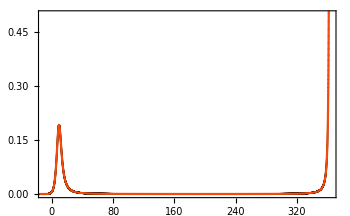
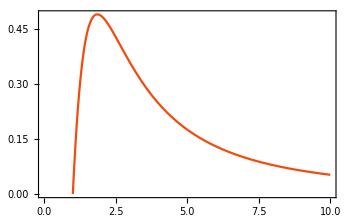

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->{{-10,imax*Δrstar},{-0,0.5}},ImageSize->350,Frame->True], Show[{VrPlot(*,Psirplot*)},ImageSize->350,Frame->True]}]
```

```mathematica
i=0;
(*lambda=5;*)
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/mass[leta,a],Evaluate[Abs[ψ[i,j]]]},{j,0,9001}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

1.0100000000000000089

General::munfl: 0.49 3.359646391720476500400667791503905332082406657777408398093982641004593449437419512684038887259124748×10^-322 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.02 2.470328229206232720882843964341106861825299013071623822127928412503377536351043759326499181808179962×10^-323 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.49 1.30186297679168464390525876920776331618193257988874575426141827338927996165700006116506506881291084×10^-320 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

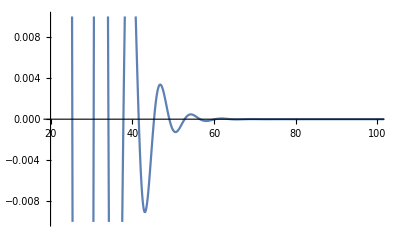

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

```mathematica
data= Table[{(j Δt)/mass[leta,a] ,ψ[i,j]},{j,0,8000}]  ;
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
(**)
Print["m = ",N[mass[leta,a]]," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["One_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[N[mass[leta,a]]]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["One_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[N[mass[leta,a]]]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.707107 , α = 1 , leta = 100 , lambda = 1

File name :

One_way_leta100a1m0.707107l1data.txt

### Final graphs ✓

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
data0=Import["One_way_leta100a1m0.707107l0data.txt","Table"]//ToExpression;
data1=Import["One_way_leta100a1m0.707107l1data.txt","Table"]//ToExpression;
data2=Import["One_way_leta100a1m0.707107l2data.txt","Table"]//ToExpression;
```

Below command : to read the number of lines a txt file has

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"One_way_leta100a1m0.707107l0data.txt","One_way_leta100a1m0.707107l1data.txt","One_way_leta100a1m0.707107l2data.txt"}
```

{8001,8001,8001}

```mathematica
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
```

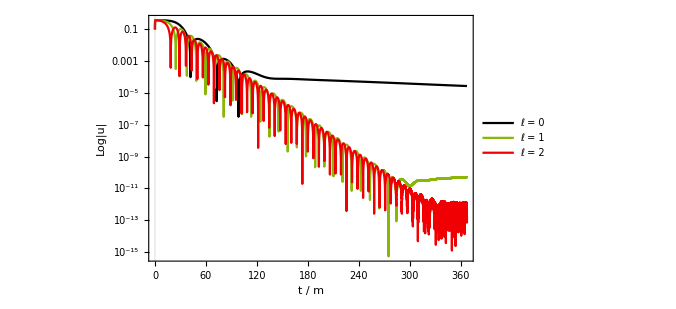

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[;;8000,;;]],data1[[;;8000,;;]],data2[[start;;8000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["ℓ = 0",15],Style["ℓ = 1",15],Style["ℓ = 2",15]},{Scaled[{0.03,0.02}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,350},{-1.3,-30}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
Block[{ε=1,leta},
times=100;
V1=Plot[{Veff[r,2]/.leta->5},{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 5",15]},{0.798,0.7}]},PlotStyle->colorlist[[1]],Frame->True];
V2=Plot[{Veff[r,2]/.leta->10 },{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 10",15]},{0.8,0.62}]},PlotStyle->colorlist[[2]],Frame->True];
]
```

```mathematica
Show[{V1,V2},PlotRange->{{-90,90},All},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\Grav_Petrurbations_NMDC\\3rd Run-Plots\\"];
Export["GP_Rin_leta01manymasses.pdf",NotebookRead[PreviousCell[]]]
```

GP_Rin_leta01manymasses.pdf

## Setup - leta = 10

### lambda = 2

```mathematica
FDrin[-100,xstarmax-10^-6,2000,500,2]
```

leta = 10, m = 0.707121, lambda = 2

r_horizon = 1.

Location of Gaussian's center = 1.0100000000000000088817841970012523233890533447265625

# of Iterations in space = 2000

(r_*)^max =  46.5623109152775679640639673701928248057991854872149444130025888336831203711168582444657808316464855  , r^max =  5.9999999999999955477×10^8

(r_*)^min =  -100  ,  r^min =  1.0000000000000000000

I_max = 635

I_min = -1364

Space Discretization step = 0.0732812

t_final/M = 707.093

# of Iterations in time = J_max = 9747

Time Discretization step = 0.0512968

Δt/(Δr_*) = 0.7

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin+100,imax-10}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

```mathematica
(*Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];*)
```

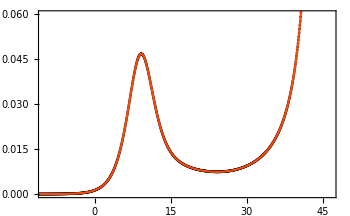
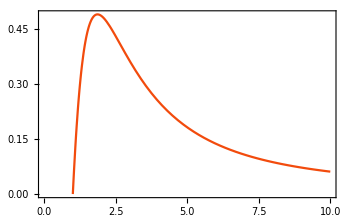

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->{{-10,imax*Δrstar},{-0,0.06}},ImageSize->350,Frame->True], Show[{VrPlot(*,Psirplot*)},ImageSize->350,Frame->True]}]
```

1.0100000000000000089

General::munfl: 0.49 9.06539583116435335019302248996716426260515817176175640419491092909583507448315147272025018347×10^-465979 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.02 4.27197047474085787482587492470951310457199495483472840223423473105204372408511682919003423197×10^-466445 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.49 1.235164114603116360441421982170553430912649506535811911063964206251688768175521879663249590904089981×10^-322 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

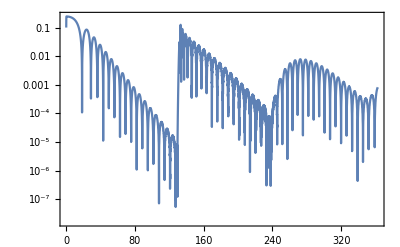

```mathematica
i=0;
(*lambda=5;*)
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/mass[leta,a],Evaluate[Abs[ψ[i,j]]]},{j,0,5000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

-Graphics-

```mathematica
data= Table[{(j Δt)/mass[leta,a] ,ψ[i,j]},{j,0,5000}]  ;
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
(**)
Print["m = ",N[mass[leta,a]]," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["One_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[N[mass[leta,a]]]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["One_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[N[mass[leta,a]]]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.707121 , α = 1 , leta = 10 , lambda = 2

File name :

One_way_leta10a1m0.707121l2data.txt

### Final graphs ✓

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
(*data0=Import["One_way_leta5a1m0.707321l0data.txt","Table"]//ToExpression;
data1=Import["One_way_leta5a1m0.707321l1data.txt","Table"]//ToExpression;*)
data2=Import["One_way_leta10a1m0.707121l2data.txt","Table"]//ToExpression;
```

Below command : to read the number of lines a txt file has

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"One_way_leta10a1m0.707121l2data.txt"}
```

{5001}

```mathematica
(*data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];*)
data2[[;;,2]]=Abs[data2[[;;,2]]];
```

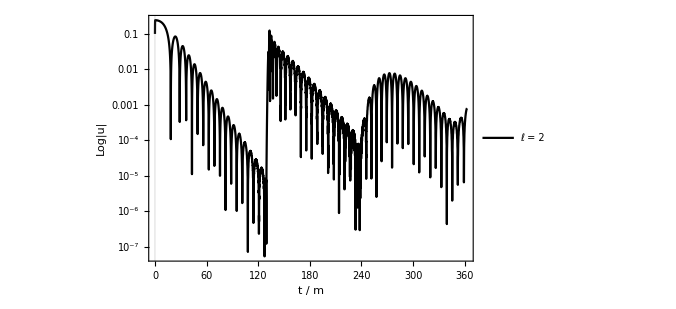

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{(*data0[[;;10000,;;]],data1[[;;8000,;;]],*)data2[[start;;5000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{(*Style["ℓ = 0",15],Style["ℓ = 1",15],*)Style["ℓ = 2",15]},{Scaled[{0.03,0.02}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,350},{-1.3,-18}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
Block[{ε=1,leta},
times=100;
V1=Plot[{Veff[r,2]/.leta->5},{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 5",15]},{0.798,0.7}]},PlotStyle->colorlist[[1]],Frame->True];
V2=Plot[{Veff[r,2]/.leta->10 },{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 10",15]},{0.8,0.62}]},PlotStyle->colorlist[[2]],Frame->True];
]
```

```mathematica
Show[{V1,V2},PlotRange->{{-90,90},All},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\Grav_Petrurbations_NMDC\\3rd Run-Plots\\"];
Export["GP_Rin_leta01manymasses.pdf",NotebookRead[PreviousCell[]]]
```

GP_Rin_leta01manymasses.pdf

## Setup - leta = 5

### lambda = 0,1,2

```mathematica
FDrin[-100,xstarmax-10^-7,2000,50,1]
```

leta = 5, m = 0.707321, lambda = 1

r_horizon = 1.

Location of Gaussian's center = 1.0100000000000000088817841970012523233890533447265625

# of Iterations in space = 2000

(r_*)^max =  27.6243428153482360496015864318927264467808687385345397106087401449100536480257304381268866015560995  , r^max =  1.4999999999999999548×10^9

(r_*)^min =  -100  ,  r^min =  1.0000000000000000000

I_max = 432

I_min = -1567

Space Discretization step = 0.0638122

t_final/M = 70.6893

# of Iterations in time = J_max = 1119

Time Discretization step = 0.0446685

Δt/(Δr_*) = 0.7

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

```mathematica
P(*siplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];*)
```

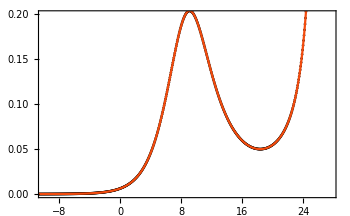
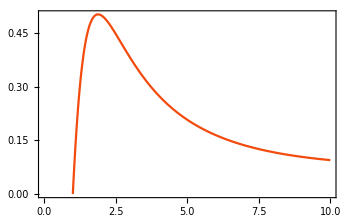

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->{{-10,imax*Δrstar},{-0,0.2}},ImageSize->350,Frame->True], Show[{VrPlot(*,Psirplot*)},ImageSize->350,Frame->True]}]
```

1.0100000000000000089

General::munfl: 0.49 3.64143767997064977213831326479444146733390973143960538801956653709707911323414609090405935622×10^-795271 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.02 1.30749303477712543266914192469587844657203630821728268457744072936818219224924014339984484772×10^-795801 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.49 7.410984687618698162648531893023320585475897039214871466383785237510132609053131277979497545424539886×10^-322 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

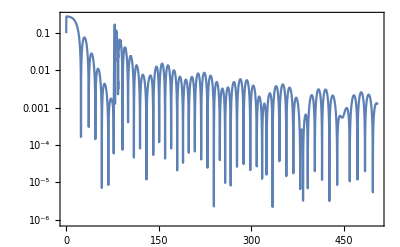

```mathematica
i=0;
(*lambda=5;*)
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/mass[leta,a],Evaluate[Abs[ψ[i,j]]]},{j,0,8000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

-Graphics-

```mathematica
data= Table[{(j Δt)/mass[leta,a] ,ψ[i,j]},{j,0,8000}]  ;
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
(**)
Print["m = ",N[mass[leta,a]]," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["One_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[N[mass[leta,a]]]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["One_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[N[mass[leta,a]]]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.707321 , α = 1 , leta = 5 , lambda = 1

File name :

One_way_leta5a1m0.707321l1data.txt

### Final graphs ✓

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
data0=Import["One_way_leta5a1m0.707321l0data.txt","Table"]//ToExpression;
data1=Import["One_way_leta5a1m0.707321l1data.txt","Table"]//ToExpression;
data2=Import["One_way_leta5a1m0.707321l2data.txt","Table"]//ToExpression;
```

Below command : to read the number of lines a txt file has

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"One_way_leta5a1m0.707321l0data.txt","One_way_leta5a1m0.707321l1data.txt","One_way_leta5a1m0.707321l2data.txt"}
```

{10001,8001,8001}

```mathematica
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
```

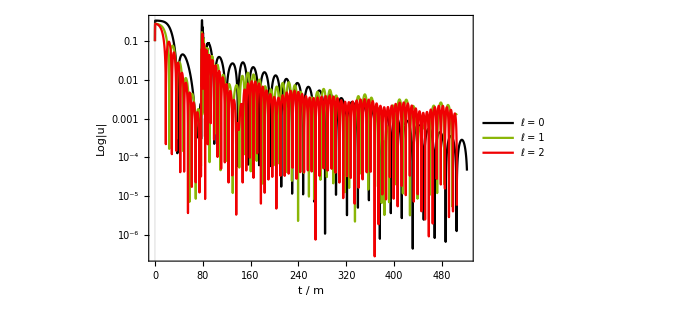

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[;;10000,;;]],data1[[;;8000,;;]],data2[[start;;8000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["ℓ = 0",15],Style["ℓ = 1",15],Style["ℓ = 2",15]},{Scaled[{0.03,0.02}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,500},{-1.3,-18}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
Block[{ε=1,leta},
times=100;
V1=Plot[{Veff[r,2]/.leta->5},{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 5",15]},{0.798,0.7}]},PlotStyle->colorlist[[1]],Frame->True];
V2=Plot[{Veff[r,2]/.leta->10 },{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 10",15]},{0.8,0.62}]},PlotStyle->colorlist[[2]],Frame->True];
]
```

```mathematica
Show[{V1,V2},PlotRange->{{-90,90},All},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\Grav_Petrurbations_NMDC\\3rd Run-Plots\\"];
Export["GP_Rin_leta01manymasses.pdf",NotebookRead[PreviousCell[]]]
```

GP_Rin_leta01manymasses.pdf

## Graphs - a = 2 , lambda = 2 & w.r.t. leta = 5,10(x)

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Two_way_data\\"];
data0=Import["Two_way_leta2a2m0.1l2data.txt","Table"]//ToExpression;
data1=Import["Two_way_leta5a2m0.1l2data.txt","Table"]//ToExpression;
data2=Import["Two_way_leta10a2m0.1l2data.txt","Table"]//ToExpression;
```

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"Two_way_leta2a2m0.1l2data.txt","Two_way_leta5a2m0.1l2data.txt","Two_way_leta10a2m0.1l2data.txt"}
```

{4001,5001,6001}

```mathematica
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
```

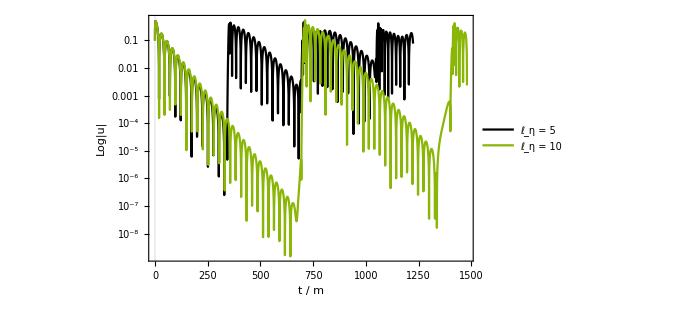

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data1[[start;;5000,;;]],data2[[start;;6000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["ℓ_η = 5",15],Style["ℓ_η = 10",15]},{Scaled[{0.78,0.15}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,1000},{2,-21}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
Block[{ε=1,m=0.1,leta,η},
times=100;
V1=Plot[{Veff[r,2]/.leta->5},{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 5",15]},{0.798,0.7}]},PlotStyle->colorlist[[1]],Frame->True];
V2=Plot[{Veff[r,2]/.leta->10 },{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 10",15]},{0.8,0.62}]},PlotStyle->colorlist[[2]],Frame->True];
]
```

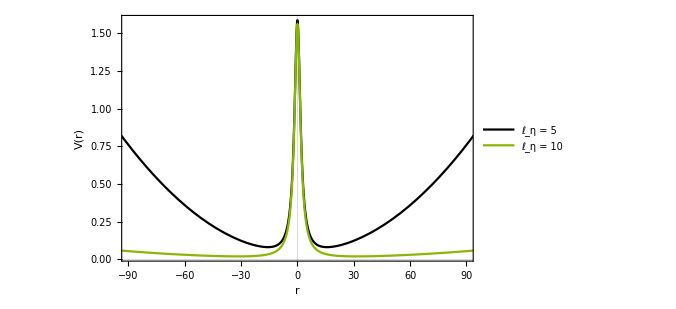

```mathematica
Show[{V1,V2},PlotRange->{{-90,90},All},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

## Setup - leta = 5 , lambda = 2 & w.r.t. a = 1,2,3 (X)

### a = 1,2(ready),3 - lambda = 2

```mathematica
FDrin[xstarmin+10^-7,xstarmax-10^-7,1000,50,2]
```

leta = 5, m = 0.1, lambda = 2

Part::partw: Part 2 of {} does not exist.

r_horizon = {}⟦1,2,1,2⟧

Location of Gaussian's center = 0.01000000000000000020816681711721685132943093776702880859375

# of Iterations in space = 1000

(r_*)^max =  17.0021935705178684166505040957721781200210795118178448093037803477261989644855402778223882761959092  , r^max =  1.4999999999999999530×10^9

(r_*)^min =  -17.0206834808150175438150909764208313868546002686313923679205475105889635258609497638901874648250097  ,  r^min =  -1.4999999999999999530×10^9

I_max = 499

I_min = -500

Space Discretization step = 0.0340229

t_final/M = 500.

# of Iterations in time = J_max = 2099

Time Discretization step = 0.023816

Δt/(Δr_*) = 0.7

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

```mathematica
Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,2,1,2⟧ in {r,{}⟦1,2,1,2⟧,10 {}⟦1,2,1,2⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[{Veff[r,2]},{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotRange→Automatic,PlotStyle→colorlist,AxesOrigin→{0,0},PlotLegends→Expressions],Plot[PsiSquare[r],{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotStyle→colorlist⟦2⟧,PlotRange→All]},ImageSize→Small].

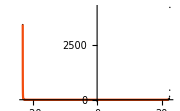
-Graphics-Show[{Plot[{Veff[r,2]},{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotRange→Automatic,PlotStyle→colorlist,AxesOrigin→{0,0},PlotLegends→Expressions],Plot[PsiSquare[r],{r,horizonsol[leta,a],10 horizonsol[leta,a]},PlotStyle→colorlist⟦2⟧,PlotRange→All]},ImageSize→Small]

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->Automatic(*{{-10,5},{-0.5,0.5}}*),ImageSize->Small], Show[{VrPlot,Psirplot},ImageSize->Small]}]
```

0.010000000000000000208

General::munfl: 1.01986 1.99153302074181209560578973202942222584301696166963923340424634052172316950356077010292997244642×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.49 1.99153302075273287971298978072367771611617067942547047362676220274832847402936521752589846000017×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.01986 4.94147587413875137199155271445927395343862835668856773713558983951061966969069686218080571664024×10^-317 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

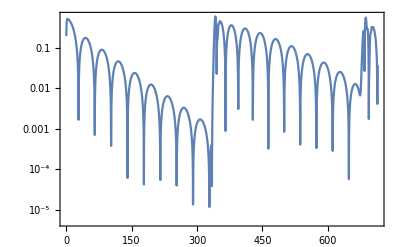

```mathematica
i=0;
(*lambda=5;*)
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/m,Evaluate[Abs[ψ[i,j]]]},{j,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

-Graphics-

```mathematica
data= Table[{(j Δt)/m ,ψ[i,j]},{j,0,3000}];
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Two_way_data\\"];
(**)
Print["m = ",m," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["Two_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[m]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["Two_way_leta"<>ToString[leta]<>"a"<>ToString[a]<>"m"<>ToString[m]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.1 , α = 3 , leta = 5 , lambda = 2

File name :

Two_way_leta5a3m0.1l2data.txt

### Final graphs ✓

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\Two_way_data\\"];
data0=Import["Two_way_leta5a1m0.1l2data.txt","Table"]//ToExpression;
data1=Import["Two_way_leta5a2m0.1l2data.txt","Table"]//ToExpression;
data2=Import["Two_way_leta5a3m0.1l2data.txt","Table"]//ToExpression;
```

Below command : to read the number of lines a txt file has

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"Two_way_leta5a1m0.1l2data.txt","Two_way_leta5a2m0.1l2data.txt","Two_way_leta5a3m0.1l2data.txt"}
```

{3001,5001,3001}

```mathematica
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
```

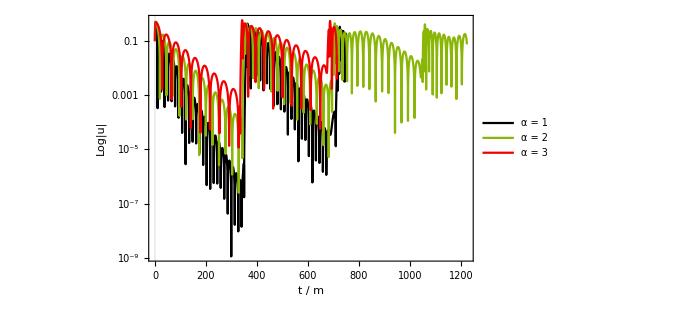

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[;;3000,;;]],data1[[;;5000,;;]],data2[[start;;3000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["α = 1",15],Style["α = 2",15],Style["α = 3",15]},{Scaled[{0.72,0.04}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,650},{0,-21}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
Block[{ε=1,m=0.1,leta=5,a},
times=100;
V1=Plot[{Veff[r,2]/.a->1},{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["α = 1",15]},{0.8,0.7}]},PlotStyle->colorlist[[1]],Frame->True];
V2=Plot[{Veff[r,2]/.a->2},{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["α = 2",15]},{0.8,0.62}]},PlotStyle->colorlist[[2]],Frame->True];
V3=Plot[{Veff[r,2]/.a->3 },{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["α = 3",15]},{0.8,0.54}]},PlotStyle->colorlist[[3]],Frame->True];
]
```

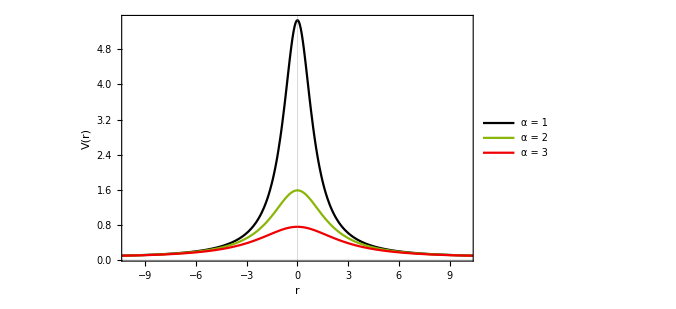

```mathematica
Show[{V1,V2,V3},PlotRange->{{-10,10},All},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\Grav_Petrurbations_NMDC\\3rd Run-Plots\\"];
Export["GP_Rin_leta01manymasses.pdf",NotebookRead[PreviousCell[]]]
```

GP_Rin_leta01manymasses.pdf

# One - way WH (new approach)

## One way wormhole : a=r_H (but not fixed on a specific value)

The approach is based on ---->

```mathematica
(* we want a = Subscript[r, H] hence, a is the value of r that solves the equation for the event horizon *)
horizontest[letain_,min_]:= NumberForm[NSolve[3 -(8 m)/(√(r^2+a^2))+(r^2+a^2)/(3 leta^2)+leta/(√(r^2+a^2))ArcTan[(√(r^2+a^2))/leta]==0/.leta->letain/.m->min/.a->r,r,Reals],200][[1,2,1,2]]
```

That way we the mass becomes  independent of the coupling leta. Meaning we have more control over  the parameter tuning . Hence, we’’ll use that definition for solving the event horizon and we’’ll set a= r_H accordingly

```mathematica
Quit[];
```

```mathematica
Clear["Global`*"];
```

## Colors for plots

```mathematica
CD3 = ColorData[3,"ColorList"];
colorlist= CD3[[#]]& /@{1,4,6,3};
newred=ColorData[16,"ColorList"][[9]];
colorlist =  Insert[colorlist,newred,3]//Append[ColorData[14,"ColorList"][[2]]]
```

{RGBColor[0., 0., 0.],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.9411764705882353, 0., 0.00784313725490196],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744]}

```mathematica
{RGBColor[0., 0., 0.],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.9411764705882353, 0., 0.00784313725490196],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882]}
```

```mathematica
ColorData[#,"ColorList"]& /@ Range[13,20]
```

{{RGBColor[0.6588235294117647, 0.4980392156862745, 0.49019607843137253],RGBColor[0.7215686274509804, 0.1843137254901961, 0.050980392156862744],RGBColor[0.803921568627451, 0.5450980392156862, 0.4588235294117647],RGBColor[0.8156862745098039, 0.6901960784313725, 0.6313725490196078],RGBColor[0.9490196078431372, 0.8745098039215686, 0.7176470588235294],RGBColor[0.3803921568627451, 0.3843137254901961, 0.6352941176470588],RGBColor[0.23137254901960785, 0.20784313725490197, 0.5529411764705883],RGBColor[0.5843137254901961, 0.5607843137254902, 0.6627450980392157],RGBColor[0.4666666666666667, 0.27450980392156865, 0.34901960784313724],RGBColor[0.596078431372549, 0.27450980392156865, 0.36470588235294116]},{RGBColor[0.8352941176470589, 0.5764705882352941, 0.5607843137254902],RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744],RGBColor[1., 0.7333333333333333, 0.2],RGBColor[0.996078431372549, 0.9490196078431372, 0.44313725490196076],RGBColor[0.7058823529411765, 0.6862745098039216, 0.30196078431372547],RGBColor[0.41568627450980394, 0.5450980392156862, 0.12156862745098039],RGBColor[0.0196078431372549, 0.20784313725490197, 0.4627450980392157],RGBColor[0.6862745098039216, 0.7215686274509804, 0.8117647058823529],RGBColor[0.42745098039215684, 0.06666666666666667, 0.1568627450980392],RGBColor[0.8549019607843137, 0.19607843137254902, 0.27450980392156865]},{RGBColor[0.40784313725490196, 0.15294117647058825, 0.13725490196078433],RGBColor[0.6588235294117647, 0.5607843137254902, 0.5333333333333333],RGBColor[0.8313725490196079, 0.43529411764705883, 0.12941176470588237],RGBColor[0.8941176470588236, 0.8274509803921568, 0.7647058823529411],RGBColor[0.9372549019607843, 0.7764705882352941, 0.3137254901960784],RGBColor[0.23921568627450981, 0.27058823529411763, 0.4627450980392157],RGBColor[0.23529411764705882, 0.1450980392156863, 0.4588235294117647],RGBColor[0.36470588235294116, 0.23921568627450981, 0.43137254901960786],RGBColor[0.2196078431372549, 0.12549019607843137, 0.18823529411764706],RGBColor[0.5529411764705883, 0.12941176470588237, 0.2235294117647059],RGBColor[0.7058823529411765, 0.2627450980392157, 0.27058823529411763]},{RGBColor[0.4549019607843137, 0.050980392156862744, 0.023529411764705882],RGBColor[0.6784313725490196, 0.3137254901960784, 0.],RGBColor[0.9058823529411765, 0.6392156862745098, 0.07058823529411765],RGBColor[0.16470588235294117, 0.41568627450980394, 0.11764705882352941],RGBColor[0.8549019607843137, 0.9607843137254902, 1.],RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333],RGBColor[0.6392156862745098, 0.5607843137254902, 0.7529411764705882],RGBColor[0.1450980392156863, 0.11372549019607843, 0.16470588235294117],RGBColor[0.9411764705882353, 0., 0.00784313725490196]},{RGBColor[0.2823529411764706, 0.22745098039215686, 0.2235294117647059],RGBColor[0.5647058823529412, 0.23137254901960785, 0.15294117647058825],RGBColor[0.6392156862745098, 0.39215686274509803, 0.3333333333333333],RGBColor[0.8627450980392157, 0.6196078431372549, 0.2627450980392157],RGBColor[0.9647058823529412, 0.788235294117647, 0.5254901960784314],RGBColor[0.4588235294117647, 0.592156862745098, 0.4627450980392157],RGBColor[0.23921568627450981, 0.45098039215686275, 0.24705882352941178],RGBColor[0.34509803921568627, 0.5803921568627451, 0.6901960784313725],RGBColor[0.1843137254901961, 0.39215686274509803, 0.49019607843137253],RGBColor[0.5686274509803921, 0.7490196078431373, 0.8431372549019608]},{RGBColor[0.7647058823529411, 0.5568627450980392, 0.5411764705882353],RGBColor[0.9921568627450981, 0.788235294117647, 0.7568627450980392],RGBColor[0.29411764705882354, 0.19215686274509805, 0.10588235294117647],RGBColor[0.37254901960784315, 0.2784313725490196, 0.19215686274509805],RGBColor[0.29411764705882354, 0.27058823529411763, 0.18823529411764706],RGBColor[0.7098039215686275, 0.6980392156862745, 0.5058823529411764],RGBColor[0.8705882352941177, 0.8784313725490196, 0.6901960784313725],RGBColor[0.27058823529411763, 0.33725490196078434, 0.28627450980392155],RGBColor[0.6980392156862745, 0.43529411764705883, 0.4470588235294118]},{RGBColor[0.5686274509803921, 0.043137254901960784, 0.],RGBColor[0.5607843137254902, 0.22745098039215686, 0.2],RGBColor[0.6627450980392157, 0.3333333333333333, 0.],RGBColor[0.8470588235294118, 0.6392156862745098, 0.42745098039215684],RGBColor[0.7686274509803922, 0.4627450980392157, 0.14901960784313725],RGBColor[0.01568627450980392, 0.19215686274509805, 0.09803921568627451],RGBColor[0.19215686274509805, 0.3686274509803922, 0.27450980392156865],RGBColor[0.4, 0.5254901960784314, 0.4588235294117647],RGBColor[0.06666666666666667, 0.15294117647058825, 0.20784313725490197]},{RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098],RGBColor[0.9019607843137255, 0.19607843137254902, 0.12941176470588237],RGBColor[0.3568627450980392, 0.054901960784313725, 0.01568627450980392],RGBColor[0.6823529411764706, 0.41568627450980394, 0.],RGBColor[0.8352941176470589, 0.6274509803921569, 0.08627450980392157],RGBColor[0.9803921568627451, 0.7803921568627451, 0.25882352941176473],RGBColor[1., 0.9058823529411765, 0.6549019607843137],RGBColor[0.3843137254901961, 0.6, 0.8784313725490196],RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784],RGBColor[0.12549019607843137, 0.36470588235294116, 0.6784313725490196]}}

## Metric ,V_eff , Horizon definitions

```mathematica
(*metric*) 
F[x_]:=SetPrecision[(3 -(8 m)/x+x^2/(3 leta^2)+leta/x ArcTan[x/leta]),20];
(*I dont include the minus sign on the gtt definition *)
gtt[x_]:=SetPrecision[ 1/4 F[√(x^2+a^2)],20];
grr[x_]:= SetPrecision[((x^2+a^2+2 leta^2)^2)/((x^2+a^2+leta^2)^2 F[√(x^2+a^2)]),20];
(**)
gθθ[x_]:=SetPrecision[x^2+a^2,20];
p[x_]:=SetPrecision[ √gθθ[x],20];
PsiSquare[x_]:=SetPrecision[-ε/(8 π leta^2)*(x^2 grr[x])/(x^2+leta^2),20];
(*useful definitions (for "easier" calculations) *)
(*h[x_]:=SetPrecision[√(gtt[x]/grr[x]),20];*)
(* η=-leta^2/ε;*)

(*potential*)
Veff[x_,lam_]:= Evaluate[SetPrecision[gtt[x]/p[x]^2 lam(lam+1)+1/(2 grr[x]^2 p[x])( 2 gtt[x] grr [x] D[p[x],{x,2}]+grr[x]  D[gtt[x],x]  D[p[x],x] -gtt[x] D[grr[x],x]   D[p[x],x] )  ,100]] ;
```

```mathematica
(* we want a = Subscript[r, H] hence, a is the value of r that solves the equation for the event horizon *)
horizonsol[letain_,min_]:=
Block[{a}, 
NumberForm[NSolve[3 -(8 min)/(√(r^2+a^2))+(r^2+a^2)/(3 letain^2)+letain/(√(r^2+a^2))ArcTan[(√(r^2+a^2))/letain]==0(*/.leta->letain/.m->min*)/.a->r,r,Reals],200][[1,2,1,2]]
]
```

```mathematica
horizonsol[1,#]&/@{0.1,1,2,3}
horizonsol[#,1]&/@{0.1,1,2,3}
```

{0.14141,1.22753,1.91751,2.37559}

{0.402596,1.22753,1.37674,1.4039}

```mathematica
horizonsol[5,10]
```

9.58756

Functions to produce plots wrt lambdas & mass.   Use showVeffPlot function to show these plots ... 

IMPORTANT : Βefore you run these commands, clear the global values of leta, a, m , etc.

```mathematica
plotlam[letain_,min_,lamlist_,horpos_,verpos_]:=
Block[{leta=letain,m=min,a},
(**)
Print["Horizon = ",horizonsol[leta,m]];
a=horizonsol[leta,m];
(**)
legendstyle={Style[StringTemplate["ℓ = ``"][lamlist[[1]]],15],Style[StringTemplate["ℓ = ``"][lamlist[[2]]],15],Style[StringTemplate["ℓ = ``"][lamlist[[3]]],15]};
(**)
VPlot=Plot[{Veff[r,lamlist[[1]]],Veff[r,lamlist[[2]]],Veff[r,lamlist[[3]]]},{r,horizonsol[leta,m],100},PlotRange->All,PlotTheme->"Scientific" ,PlotStyle->colorlist ,PlotLegends->{ Placed[legendstyle,{horpos,verpos}]},
ImageSize->500];
]
```

```mathematica
plotmass[letain_,mlistin_,horpos_,verpos_]:=
Block[
{ε=1,leta=letain,m,mlist=mlistin,alist,a1,a2,a3},
(*mlist={0.1,0.2,0.3};*)
alist={a1,a2,a3}=horizonsol[leta,#]&/@mlist;
times=200;
V1=Plot[{Veff[r,2]/.m->mlist[[1]]/.a->alist[[1]]},{r,alist[[1]],times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[StringTemplate["m = ``"][mlist[[1]]],15]},{horpos,verpos}]},PlotStyle->colorlist[[1]],Frame->True];
(**)
V2=Plot[{Veff[r,2]/.m->mlist[[2]]/.a->alist[[2]]},{r,alist[[2]],times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[StringTemplate["m = ``"][mlist[[2]]],15]},{horpos,Evaluate[verpos-0.08]}]},PlotStyle->colorlist[[2]],Frame->True];
(**)
V3=Plot[{Veff[r,2]/.m->mlist[[3]]/.a->alist[[3]] },{r,alist[[3]],times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style[StringTemplate["m = ``"][mlist[[3]]],15]},{horpos,Evaluate[verpos-2*0.08]}]},PlotStyle->colorlist[[3]],Frame->True];
VPlot = {V1,V2,V3};
]
```

```mathematica
showVeffPlot[left_,right_,up_,down_]:=Show[VPlot,PlotRange->{{left,right},{down,up}},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

## Analysis & FD Code Setup

## tortoise

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
leta=1;m=0.6;a=horizonsol[leta,m];ε=1;
(**)
Print["Horizon = ",horizonsol[leta,m]]
x= First[x1/. NDSolve[{x1'[xstar]==((1/4(3 -(8 m)/(√(x1[xstar]^2+a^2))+(x1[xstar]^2+a^2)/(3 leta^2)+leta/(√(x1[xstar]^2+a^2))ArcTan[(√(x1[xstar]^2+a^2))/leta]))/(((x1[xstar]^2+a^2+2 leta^2)^2)/((x1[xstar]^2+a^2+leta^2)^2)(1/(3 -(8m)/(√(x1[xstar]^2+a^2))+(x1[xstar]^2+a^2)/(3 leta^2)+leta/(√(x1[xstar]^2+a^2))ArcTan[(√(x1[xstar]^2+a^2))/leta]))) )^(1/2),x1[0]==SetPrecision[1.01*horizonsol[leta,m],200](*SetPrecision[1.01*horizonsol[leta,a],200]*)(*throat @ x=0SetPrecision[1.01*horizonsol[leta,a],200]*)},
x1,{xstar,-10000,10000},Method->Automatic,
MaxSteps->10^7,
WorkingPrecision->100,
AccuracyGoal->50,
PrecisionGoal->20,
InterpolationOrder->All]]
{xstarmin,xstarmax}=InterpolatingFunctionDomain[x][[1]]
x[#]& /@{xstarmin,xstarmax}
```

Horizon = 0.811385

NDSolve::precw: The precision of the differential equation ({{x1'[xstar]==1/2 √((Plus[«2»]^2 Plus[«4»]^2)/Plus[«2»]^2),x1[0]==0.8194988909559486334188704859116114675998687744140625},{},{},{},{}}) is less than WorkingPrecision (100.).

NDSolve::ndsz: At xstar == 7.138248483933828866056651850095663350068544042302392953450570561539217825663229963757474866583363528, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[{{-10000.00000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000, 7.138248483933828866056651850095663350068544042302392953450570561539217825663229963757474866583363528}}, <>]

{-10000.,7.138248483933828866056651850095663350068544042302392953450570561539217825663229963757474866583363528}

{0.8113850405504442524179534235107717137175445842133835801034537824102692351131808870053573821288267,2.×10^87}

## Further checking r_*vs V_eff

Now we just check the general behavior of the r(r_*) function and how it may affect the V_eff

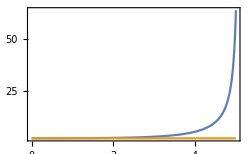

```mathematica
Plot[{x[xstar],horizonsol[leta,m]},{xstar,0,5},PlotRange->All,ImageSize->250,Frame->True]
```

Horizon = 1.91751

a = 1.91751

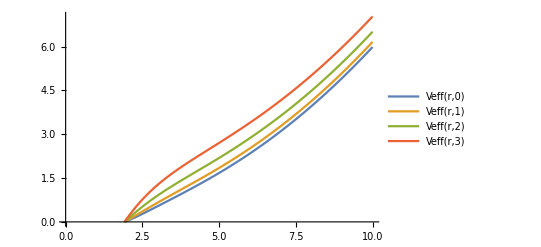
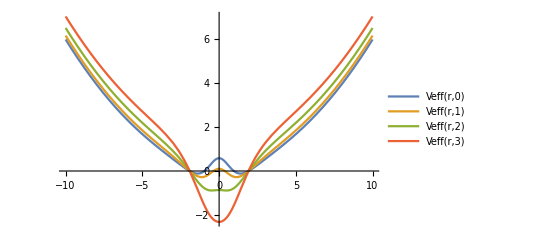

```mathematica
Block[{leta=1,m=2,ε=1 },
Print["Horizon = ",horizonsol[leta,m]];
Print["a = ",a];
VrPlot=Plot[{Veff[r,0],Veff[r,1],Veff[r,2],Veff[r,3]},{r,horizonsol[leta,m],10},PlotRange->Automatic(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
VrPlot2=Plot[{Veff[r,0],Veff[r,1],Veff[r,2],Veff[r,3]},{r,-10,10},PlotRange->Automatic(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
Show[VrPlot]
Show[VrPlot2]
]
```

## Finite Difference Code

### FD - Code

Finite Difference - Implementation CODE

```mathematica
FDrin[start_,stop_,iter_,tfinal_,lam_]:=(
Clear[ψ,Length1,Δrstar,Δt,imax,imin,lambda,,jmax,σ,center,ψinit2,ψinit,V,ψinit3,ψbound,ψbound2];

(*Discretization setup*)
(*rstarmax=stop; rstarmin=start;*) Length1=stop-start;
 Δrstar=Length1/iter; Δt=Δrstar*0.7;
imax=IntegerPart[N[stop/Δrstar]];imin=IntegerPart[N[start/Δrstar]];
jmax = IntegerPart[N[tfinal/Δt]];
(**)
lambda=lam;
(*-------messages to check code behavior-------*)
printstyle={Blue,14,Italic,FontFamily->"Courier"};
Print["leta = ",leta,", m = ",N[m] , ", lambda = ",lambda];
Print["r_horizon = ",horizonsol[leta,m]];
Print[Style["Location of Gaussian's center = ",Blue,14,Italic,FontFamily->"Courier"],Style[x[0],Blue,14,Italic,FontFamily->"Courier"]];
(**)
Print[Style["# of Iterations in space = ",printstyle],Style[iter,14,Blue,Italic]];
(**)
Print[ Style["(r_*)^max =  ",printstyle],Style[stop " , ",printstyle],
Style["r^max =  ",printstyle], Style[NumberForm[ x[stop],20],printstyle]];
Print[ Style["(r_*)^min =  ",printstyle],Style[start " , ",printstyle],
Style[" r^min =  ",printstyle], Style[NumberForm[ x[start],20],printstyle]];
(**)
Print[Style[ "I_max = ",printstyle],Style[imax,printstyle]];
Print[Style[ "I_min = ",printstyle],Style[imin,printstyle]];
(**)
Print[Style["Space Discretization step = ",printstyle],Style[N[Δrstar],printstyle]];
Print[Style["t_final/M = ",printstyle],Style[N[tfinal/N[m]],printstyle]];
Print[Style[ "# of Iterations in time = J_max = ",printstyle],Style[jmax,printstyle]];
Print[Style["Time Discretization step = ",printstyle],Style[Δt,printstyle]];
Print[Style["Δt/(Δr_*) = ",printstyle],Style[N[Δt/Δrstar],printstyle]];(*--V effective & functions A(r)/B(r)Discretization--*)
(*Do[V[i]=Veff[r[i*Δrstar],lam],{i,imin,imax}];
Do[Adis[i]=A[r[i*Δrstar]],{i,imin,imax}];
Do[Bdis[i]=B[r[i*Δrstar]],{i,imin,imax}];*)
(*interVeff=Interpolation[Table[{rstar,Veff[r[rstar],lam]},{rstar,-1000,rstarmax,0.1}],InterpolationOrder->3];*)

V[i_]:=V[i]=(*interVeff[i*Δrstar]*)SetPrecision[ Veff[x[i*Δrstar],lam],100];

(*--------Initial Condtions--------*) 
σ=0.1;center=0;
ψ[i_,0]:=ψinit2[rstar] /.rstar->i Δrstar  ;
ψinit2[rstar_]:=SetPrecision[1/10 Exp[-(rstar-center)^2/(2 σ^2)],100];
ψ[i_,-1]:=ψinit[x[rstar]]  /.rstar->i Δrstar ;
ψinit[x[rstar_]]=0; 
(*-------Boundary Condition(s)-------*)
ψ[imax,j_]:=ψ[imax,j]= 0;
(*ψ[imin,j_]:=ψ[imin,j]= 0;*)(*comment out when ther is a horizon*)
(*--------Iterating Scheme---------*)

(*SetPrecision[ψ[imax-1,j-1]+(((Adis[imax-1] Bdis[imax-1]+Adis[imax] Bdis[imax])/2 Δt-Δrstar)/((Adis[imax-1] Bdis[imax-1]+Adis[imax] Bdis[imax])/2 Δt+Δrstar))*( ψ[imax-1,j]-ψ[imax,j-1]),40];*)ψ[i_,j_]:=ψ[i,j]=SetPrecision[ -ψ[i,j-2]+(Δt/Δrstar)^2(ψ[i+1,j-1]+ψ[i-1,j-1]) + (2-2 (Δt/Δrstar)^2-V[i] Δt^2) ψ[i,j-1] ,100] ;);
```

## Numerical Results - simulations 2 (new approach)

## Setup - leta = 1 , m = 0.06 , lambda=2

```mathematica
FDrin[-10,xstarmax-10^-7,800,50,2]
```

Clear::wrsym: Symbol Null is Protected.

leta = 1, m = 0.06, lambda = 2

r_horizon = 0.0848519

Location of Gaussian's center = 0.08570046241145778953551825907197780907154083251953125

# of Iterations in space = 800

(r_*)^max =  4.50440485607095581147930928999019250413687356181483753691729287089219111782946925603956839781650573  , r^max =  5.9999999999999955490×10^7

(r_*)^min =  -10  ,  r^min =  0.084851942981641413181

I_max = 248

I_min = -551

Space Discretization step = 0.0181305

t_final/M = 833.333

# of Iterations in time = J_max = 3939

Time Discretization step = 0.0126914

Δt/(Δr_*) = 0.7

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

```mathematica
(*Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];*)
```

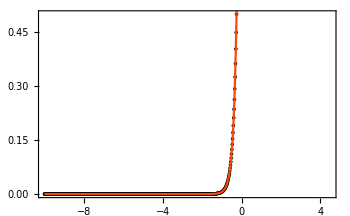
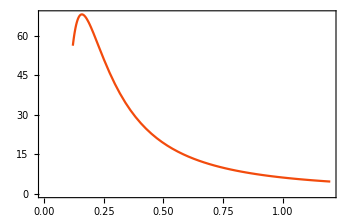

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->{{-10,imax*Δrstar},{-0,0.5}},ImageSize->350,Frame->True], Show[{VrPlot(*,Psirplot*)},ImageSize->350,Frame->True]}]
```

0.085700462411457789536

General::munfl: 0.49 2.0314988831267525180664632849561687707294784885711000937283341150607297347213914287811028810085×10^-7125 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.02 1.0940385218954253289063938549710995243488482435159170698450803609688087980145919014960541988603×10^-7139 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.49 9.881312916824930883531375857364427447301196052286495288511713650013510145404175037305996727232719848×10^-324 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

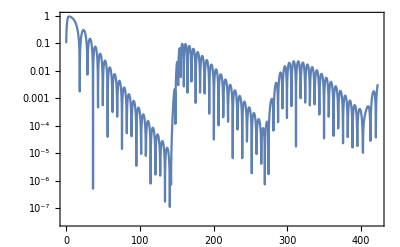

```mathematica
i=0;
(*lambda=5;*)
Offpaclet:ref/Off[General::munfl];
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/m,Evaluate[Abs[ψ[i,j]]]},{j,0,2000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

-Graphics-

```mathematica
data= Table[{(j Δt)/m ,ψ[i,j]},{j,0,2000}]  ;
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
(**)
Print["m = ",m," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.06 , α = 0.0848519 , leta = 1 , lambda = 2

File name :

One_way_m0.06leta1a0.0848519l2data.txt

## Setup - leta = 1 , m = 0.1

### lambda = 0,1,2

```mathematica
FDrin[-10,xstarmax-10^-7,800,50,2]
```

Clear::wrsym: Symbol Null is Protected.

leta = 1, m = 0.1, lambda = 2

r_horizon = 0.14141

Location of Gaussian's center = 0.1428244638706077374035174898381228558719158172607421875

# of Iterations in space = 800

(r_*)^max =  5.04278944570910301667663604489768422926230692521522403760380786911085172966480570890289963454146151  , r^max =  5.9999999999999955419×10^7

(r_*)^min =  -10  ,  r^min =  0.14141036026792846368

I_max = 268

I_min = -531

Space Discretization step = 0.0188035

t_final/M = 500.

# of Iterations in time = J_max = 3798

Time Discretization step = 0.0131624

Δt/(Δr_*) = 0.7

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

```mathematica
(*Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];*)
```

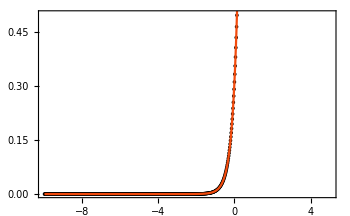
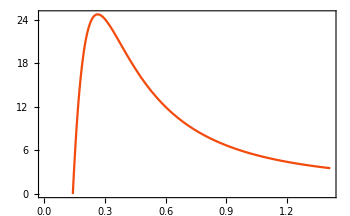

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->{{-10,imax*Δrstar},{-0,0.5}},ImageSize->350,Frame->True], Show[{VrPlot(*,Psirplot*)},ImageSize->350,Frame->True]}]
```

0.14282446387060773740

General::munfl: 0.49 4.4512963154180012783684261462250077243333790556360172719833892019441580870896222167220893093362×10^-7664 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.02 1.9987834104385130946577132014253234151682860708018322358318076109258089700233649741842584697069×10^-7679 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.49 4.8991549441618007320548561500812831283719330027236443640441076276766983300913899834963131773619825×10^-320 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

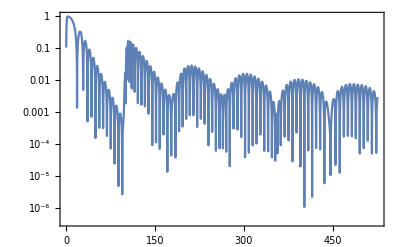

```mathematica
i=0;
(*lambda=5;*)
Offpaclet:ref/Off[General::munfl];
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/m,Evaluate[Abs[ψ[i,j]]]},{j,0,4000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

-Graphics-

```mathematica
data= Table[{(j Δt)/m ,ψ[i,j]},{j,0,4000}]  ;
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
(**)
Print["m = ",m," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.1 , α = 0.14141 , leta = 1 , lambda = 2

File name :

One_way_m0.1leta1a0.14141l2data.txt

### Final graphs ✓

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
data0=Import["One_way_m0.1leta1a0.14141l0data.txt","Table"]//ToExpression;
data1=Import["One_way_m0.1leta1a0.14141l1data.txt","Table"]//ToExpression;
data2=Import["One_way_m0.1leta1a0.14141l2data.txt","Table"]//ToExpression;
```

Below command : to read the number of lines a txt file has

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"One_way_m0.1leta1a0.14141l0data.txt","One_way_m0.1leta1a0.14141l1data.txt","One_way_m0.1leta1a0.14141l2data.txt"}
```

{4001,4001,4001}

```mathematica
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
```

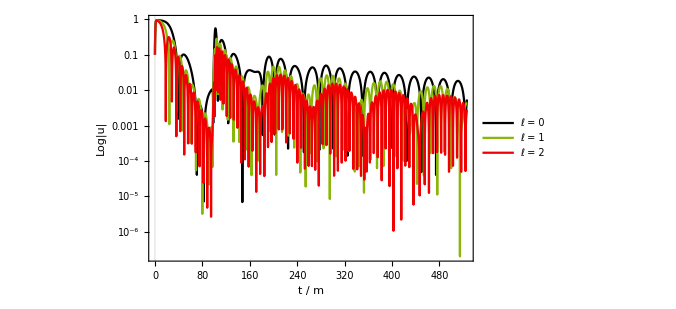

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[;;4000,;;]],data1[[;;4000,;;]],data2[[start;;4000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["ℓ = 0",15],Style["ℓ = 1",15],Style["ℓ = 2",15]},{Scaled[{0.03,0.05}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{5,350},{-0.5,-17}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
plotlam[1,0.1,{0,1,2},.85,.2];
```

Horizon = 0.14141

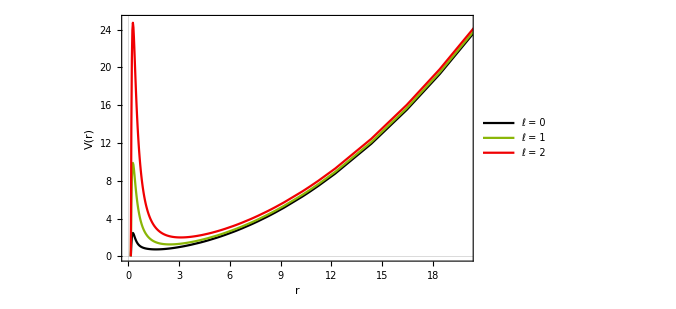

```mathematica
Show[VstarPlot, PlotRange->{{0.,20},{0,25}},
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
Block[{ε=1,leta},
times=100;
V1=Plot[{Veff[r,2]/.leta->5},{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 5",15]},{0.798,0.7}]},PlotStyle->colorlist[[1]],Frame->True];
V2=Plot[{Veff[r,2]/.leta->10 },{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 10",15]},{0.8,0.62}]},PlotStyle->colorlist[[2]],Frame->True];
]
```

```mathematica
Show[{V1,V2},PlotRange->{{-90,90},All},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\Grav_Petrurbations_NMDC\\3rd Run-Plots\\"];
Export["GP_Rin_leta01manymasses.pdf",NotebookRead[PreviousCell[]]]
```

GP_Rin_leta01manymasses.pdf

## Setup - leta = 1 , m = 0.12

### lambda = 0,1,2

```mathematica
FDrin[-10,xstarmax-10^-7,500,50,2]
```

Clear::wrsym: Symbol Null is Protected.

leta = 1, m = 0.12, lambda = 2

r_horizon = 0.212051

Location of Gaussian's center = 0.2141719477027393125911913784875650890171527862548828125

# of Iterations in space = 500

(r_*)^max =  4.88843417274714099663768117197011716828822791452729523803938207827923653947844586408997371512490971  , r^max =  5.9999999999999955461×10^7

(r_*)^min =  -10  ,  r^min =  0.21205143336904881172

I_max = 164

I_min = -335

Space Discretization step = 0.0297769

t_final/M = 416.667

# of Iterations in time = J_max = 2398

Time Discretization step = 0.0208438

Δt/(Δr_*) = 0.7

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

```mathematica
(*Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];*)
```

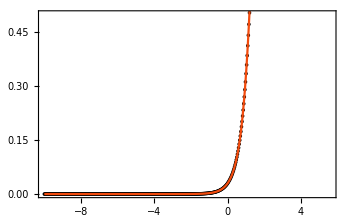
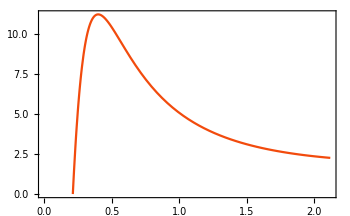

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->{{-10,imax*Δrstar},{-0,0.5}},ImageSize->350,Frame->True], Show[{VrPlot(*,Psirplot*)},ImageSize->350,Frame->True]}]
```

0.21417194770273931259

General::munfl: 1.01892 2.87336543618193253571812189209397874393304762586579547785181844593884025891020573547716946004363×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.49 2.87336543658053346528575106381012789328382097820717763162551960053576157708004431653092336933573×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.01888 3.53767720737738985956583731250182317386199003024561138932460441949205050719188507727318438854952×10^-317 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

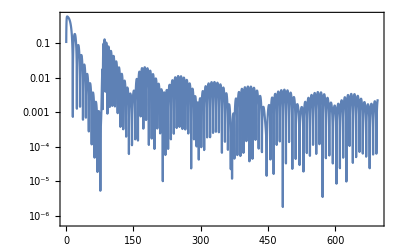

```mathematica
i=0;
(*lambda=5;*)
Offpaclet:ref/Off[General::munfl];
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/m,Evaluate[Abs[ψ[i,j]]]},{j,0,4000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

-Graphics-

```mathematica
data= Table[{(j Δt)/m ,ψ[i,j]},{j,0,4000}]  ;
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
(**)
Print["m = ",m," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.12 , α = 0.11232 , leta = 1 , lambda = 2

File name :

One_way_m0.12leta1a0.11232l2data.txt

### Final graphs ✓

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
data0=Import["One_way_m0.12leta1a0.11232l0data.txt","Table"]//ToExpression;
data1=Import["One_way_m0.12leta1a0.11232l1data.txt","Table"]//ToExpression;
data2=Import["One_way_m0.12leta1a0.11232l2data.txt","Table"]//ToExpression;
```

Below command : to read the number of lines a txt file has

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"One_way_m0.12leta1a0.11232l0data.txt","One_way_m0.12leta1a0.11232l1data.txt","One_way_m0.12leta1a0.11232l2data.txt"}
```

{4001,4001,4001}

```mathematica
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
```

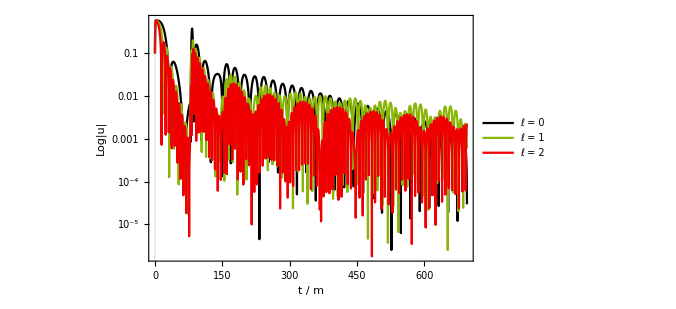

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[;;4000,;;]],data1[[;;4000,;;]],data2[[start;;4000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["ℓ = 0",15],Style["ℓ = 1",15],Style["ℓ = 2",15]},{Scaled[{0.03,0.05}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{5,350},{-0.5,-17}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
plotlam[1,0.12,{0,1,2},.85,.2];
```

Horizon = 0.169679

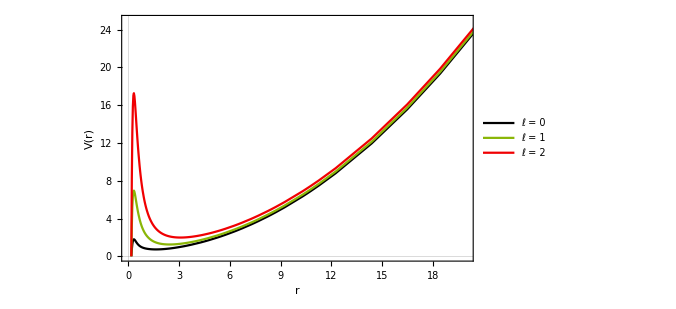

```mathematica
Show[VstarPlot, PlotRange->{{0.,20},{0,25}},
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
Block[{ε=1,leta},
times=100;
V1=Plot[{Veff[r,2]/.leta->5},{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 5",15]},{0.798,0.7}]},PlotStyle->colorlist[[1]],Frame->True];
V2=Plot[{Veff[r,2]/.leta->10 },{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 10",15]},{0.8,0.62}]},PlotStyle->colorlist[[2]],Frame->True];
]
```

```mathematica
Show[{V1,V2},PlotRange->{{-90,90},All},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\Grav_Petrurbations_NMDC\\3rd Run-Plots\\"];
Export["GP_Rin_leta01manymasses.pdf",NotebookRead[PreviousCell[]]]
```

GP_Rin_leta01manymasses.pdf

## Setup - leta = 1 , m = 0.13

### lambda = 0,1,2

```mathematica
FDrin[-10,xstarmax-10^-7,500,50,2]
```

Clear::wrsym: Symbol Null is Protected.

leta = 1, m = 0.13, lambda = 2

r_horizon = 0.183808

Location of Gaussian's center = 0.1856458034608486074024114031999488361179828643798828125

# of Iterations in space = 500

(r_*)^max =  5.39889421305251235638917980235905614106744397301962379535799785435502324084253090652487355966693122  , r^max =  5.9999999999999955345×10^7

(r_*)^min =  -10  ,  r^min =  0.18380772619886116424

I_max = 175

I_min = -324

Space Discretization step = 0.0307978

t_final/M = 384.615

# of Iterations in time = J_max = 2319

Time Discretization step = 0.0215585

Δt/(Δr_*) = 0.7

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

```mathematica
(*Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];*)
```

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->{{-10,imax*Δrstar},{-0,0.5}},ImageSize->350,Frame->True], Show[{VrPlot(*,Psirplot*)},ImageSize->350,Frame->True]}]
```

-Graphics--Graphics-

0.18564580346084860740

General::munfl: 0.49 2.7652096977315107167306299639922249881576462767401257969284125445378964116826272468351287427308×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.01908 2.48648665154866123283349953030642977136420410957405858828533329305720197777186318776354092267478×10^-313 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.49 2.4864866516999209442597642015544600237266493398840321467141382625866348463290189219857256953067×10^-313 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

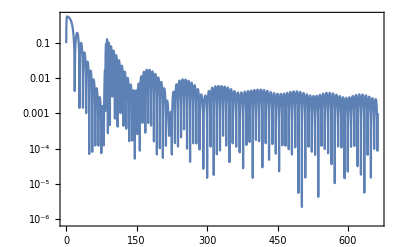

```mathematica
i=0;
(*lambda=5;*)
Offpaclet:ref/Off[General::munfl];
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/m,Evaluate[Abs[ψ[i,j]]]},{j,0,4000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

-Graphics-

```mathematica
data= Table[{(j Δt)/m ,ψ[i,j]},{j,0,4000}]  ;
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
(**)
Print["m = ",m," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.13 , α = 0.183808 , leta = 1 , lambda = 2

File name :

One_way_m0.13leta1a0.183808l2data.txt

### Final graphs ✓

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
data0=Import["One_way_m0.13leta1a0.183808l0data.txt","Table"]//ToExpression;
data1=Import["One_way_m0.13leta1a0.183808l1data.txt","Table"]//ToExpression;
data2=Import["One_way_m0.13leta1a0.183808l2data.txt","Table"]//ToExpression;
```

Below command : to read the number of lines a txt file has

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"One_way_m0.13leta1a0.183808l0data.txt","One_way_m0.13leta1a0.183808l1data.txt","One_way_m0.13leta1a0.183808l2data.txt"}
```

{4001,4001,4001}

```mathematica
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
```

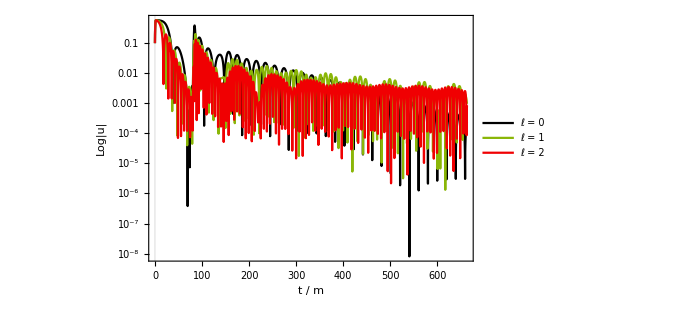

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[;;4000,;;]],data1[[;;4000,;;]],data2[[start;;4000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["ℓ = 0",15],Style["ℓ = 1",15],Style["ℓ = 2",15]},{Scaled[{0.03,0.05}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{5,350},{-0.5,-17}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
plotlam[1,0.13,{0,1,2},.85,.2];
```

Horizon = 0.183808

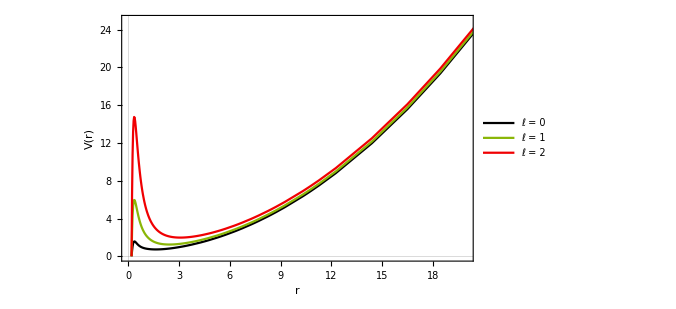

```mathematica
Show[VstarPlot, PlotRange->{{0.,20},{0,25}},
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
Block[{ε=1,leta},
times=100;
V1=Plot[{Veff[r,2]/.leta->5},{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 5",15]},{0.798,0.7}]},PlotStyle->colorlist[[1]],Frame->True];
V2=Plot[{Veff[r,2]/.leta->10 },{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 10",15]},{0.8,0.62}]},PlotStyle->colorlist[[2]],Frame->True];
]
```

```mathematica
Show[{V1,V2},PlotRange->{{-90,90},All},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\Grav_Petrurbations_NMDC\\3rd Run-Plots\\"];
Export["GP_Rin_leta01manymasses.pdf",NotebookRead[PreviousCell[]]]
```

GP_Rin_leta01manymasses.pdf

## Setup - leta = 1 , m = 0.25

### lambda = 0,1,2

```mathematica
FDrin[-10,xstarmax-10^-7,500,50,2]
```

Clear::wrsym: Symbol Null is Protected.

leta = 1, m = 0.25, lambda = 2

r_horizon = 0.352625

Location of Gaussian's center = 0.356151749471871059693484085073578171432018280029296875

# of Iterations in space = 500

(r_*)^max =  6.45785450870745819347099712687614464578487543189246306554689383913042905725396293169166439413380883  , r^max =  5.9999999999999954842×10^7

(r_*)^min =  -10  ,  r^min =  0.35262549494756434366

I_max = 196

I_min = -303

Space Discretization step = 0.0329157

t_final/M = 200.

# of Iterations in time = J_max = 2170

Time Discretization step = 0.023041

Δt/(Δr_*) = 0.7

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

```mathematica
(*Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];*)
```

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->{{-10,imax*Δrstar},{-0,0.5}},ImageSize->350,Frame->True], Show[{VrPlot(*,Psirplot*)},ImageSize->350,Frame->True]}]
```

-Graphics--Graphics-

0.35615174947187105969

General::munfl: 1.01836 7.23745814905120257554927157792697472864970400224152947384795188380642575589323635548208902514948×10^-313 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.49 7.23745814913894387391737245209859939477504634644780970845635895881840614176470837059930315681529×10^-313 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.0184 2.66024567875315756801681766216645134208223969838863639312841600513382908387850357251552817245906×10^-318 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

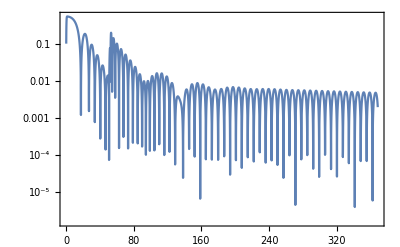

```mathematica
i=0;
(*lambda=5;*)
Offpaclet:ref/Off[General::munfl];
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/m,Evaluate[Abs[ψ[i,j]]]},{j,0,4000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

-Graphics-

```mathematica
data= Table[{(j Δt)/m ,ψ[i,j]},{j,0,4000}]  ;
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
(**)
Print["m = ",m," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.25 , α = 0.352625 , leta = 1 , lambda = 2

File name :

One_way_m0.25leta1a0.352625l2data.txt

### Final graphs ✓

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
data0=Import["One_way_m0.25leta1a0.352625l0data.txt","Table"]//ToExpression;
data1=Import["One_way_m0.25leta1a0.352625l1data.txt","Table"]//ToExpression;
data2=Import["One_way_m0.25leta1a0.352625l2data.txt","Table"]//ToExpression;
```

Below command : to read the number of lines a txt file has

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"One_way_m0.25leta1a0.352625l0data.txt","One_way_m0.25leta1a0.352625l1data.txt","One_way_m0.25leta1a0.352625l2data.txt"}
```

{4001,4001,4001}

```mathematica
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
```

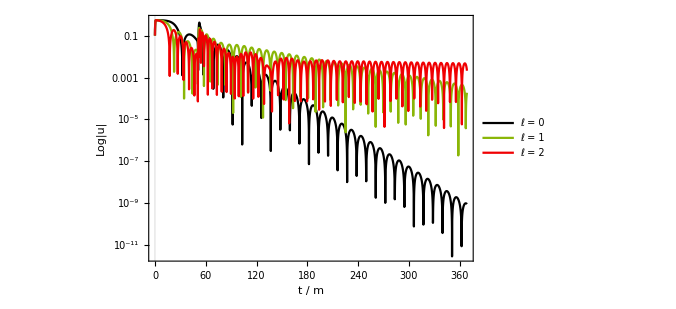

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[;;4000,;;]],data1[[;;4000,;;]],data2[[start;;4000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["ℓ = 0",15],Style["ℓ = 1",15],Style["ℓ = 2",15]},{Scaled[{0.03,0.05}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{5,350},{-0.5,-30}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
plotlam[1,0.25,{0,1,2},.85,.2];
```

Horizon = 0.352625

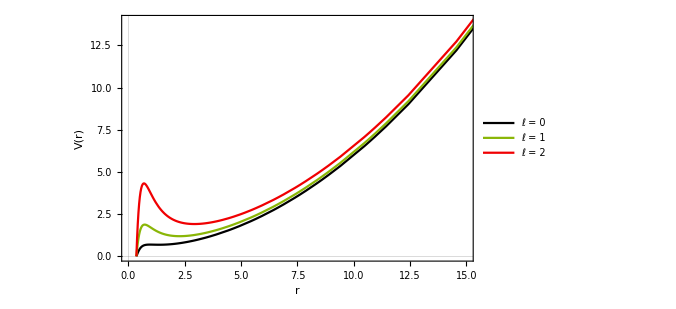

```mathematica
Show[VPlot, PlotRange->{{0,15},{0,14}},
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
Block[{ε=1,leta},
times=100;
V1=Plot[{Veff[r,2]/.leta->5},{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 5",15]},{0.798,0.7}]},PlotStyle->colorlist[[1]],Frame->True];
V2=Plot[{Veff[r,2]/.leta->10 },{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 10",15]},{0.8,0.62}]},PlotStyle->colorlist[[2]],Frame->True];
]
```

```mathematica
Show[{V1,V2},PlotRange->{{-90,90},All},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\Grav_Petrurbations_NMDC\\3rd Run-Plots\\"];
Export["GP_Rin_leta01manymasses.pdf",NotebookRead[PreviousCell[]]]
```

GP_Rin_leta01manymasses.pdf

## Setup - leta = 1 , m = 0.4 , lambda=2 ???

```mathematica
FDrin[-10,xstarmax-10^-7,800,50,2]
```

Clear::wrsym: Symbol Null is Protected.

leta = 1, m = 0.4, lambda = 2

r_horizon = 0.558121

Location of Gaussian's center = 0.56370187959654283194055324202054180204868316650390625

# of Iterations in space = 800

(r_*)^max =  7.07869766470042507028301869288336501523680121011162237020003422887489748080506112461910619553391966  , r^max =  5.9999999999999953803×10^7

(r_*)^min =  -10  ,  r^min =  0.55812071695914489692

I_max = 331

I_min = -468

Space Discretization step = 0.0213484

t_final/M = 125.

# of Iterations in time = J_max = 3345

Time Discretization step = 0.0149439

Δt/(Δr_*) = 0.7

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

```mathematica
(*Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];*)
```

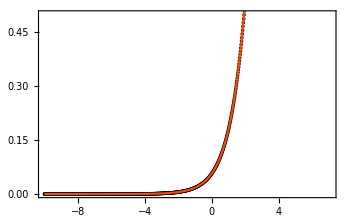
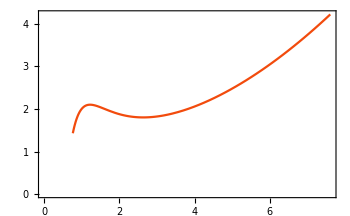

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->{{-10,imax*Δrstar},{-0,0.5}},ImageSize->350,Frame->True], Show[{VrPlot(*,Psirplot*)},ImageSize->350,Frame->True]}]
```

0.56370187959654283194

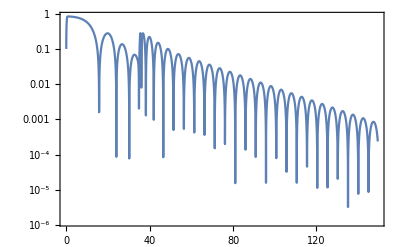

```mathematica
i=0;
(*lambda=5;*)
Offpaclet:ref/Off[General::munfl];
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/m,Evaluate[Abs[ψ[i,j]]]},{j,0,4000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

-Graphics-

```mathematica
data= Table[{(j Δt)/m ,ψ[i,j]},{j,0,8000}]  ;
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
(**)
Print["m = ",m," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.6 , α = 0.811385 , leta = 1 , lambda = 2

File name :

One_way_m0.6leta1a0.811385l2data.txt

## Setup - leta = 1 , m = 0.6 , lambda=2

```mathematica
FDrin[-10,xstarmax-10^-7,800,50,2]
```

Clear::wrsym: Symbol Null is Protected.

leta = 1, m = 0.6, lambda = 2

r_horizon = 0.811385

Location of Gaussian's center = 0.8194988909559486334188704859116114675998687744140625

# of Iterations in space = 800

(r_*)^max =  7.13824838393382886605665185009566335006854404230239295345057056153921782566322996375747486658336353  , r^max =  5.9999999999999951873×10^7

(r_*)^min =  -10  ,  r^min =  0.81138533630173173427

I_max = 333

I_min = -466

Space Discretization step = 0.0214228

t_final/M = 83.3333

# of Iterations in time = J_max = 3334

Time Discretization step = 0.014996

Δt/(Δr_*) = 0.7

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

```mathematica
(*Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];*)
```

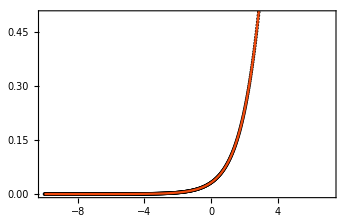
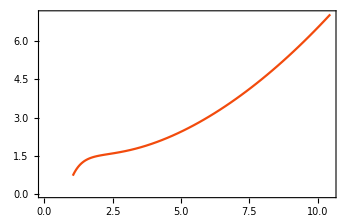

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->{{-10,imax*Δrstar},{-0,0.5}},ImageSize->350,Frame->True], Show[{VrPlot(*,Psirplot*)},ImageSize->350,Frame->True]}]
```

0.81949889095594863342

General::munfl: 1.01977 2.00865265254312367529364489543236482086928446702516572316553105726768501891344193937541581585684×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.49 2.00865282922785731669113684375779900868497393214394525954378950896494944192624452583250254047939×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.01977 6.09561628367177400517030270543391965493702348682676313645300050419039747410869424201053932627199×10^-314 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

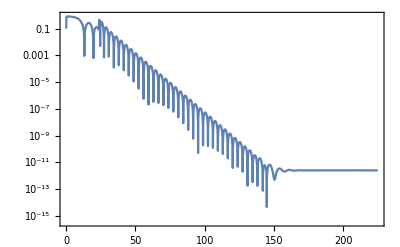

```mathematica
i=0;
(*lambda=5;*)
Offpaclet:ref/Off[General::munfl];
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/m,Evaluate[Abs[ψ[i,j]]]},{j,0,9000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

-Graphics-

```mathematica
data= Table[{(j Δt)/m ,ψ[i,j]},{j,0,9000}]  ;
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
(**)
Print["m = ",m," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 0.6 , α = 0.811385 , leta = 1 , lambda = 2

File name :

One_way_m0.6leta1a0.811385l2data.txt

## Setup - leta = 1 , m = 1

### lambda = 0,1,2

```mathematica
FDrin[-100,xstarmax-10^-7,8000,50,0]
```

Clear::wrsym: Symbol Null is Protected.

leta = 1, m = 1., lambda = 0

r_horizon = 1.22753

Location of Gaussian's center = 1.2398003637281209687870386915164999663829803466796875

# of Iterations in space = 8000

(r_*)^max =  6.46876750867336798105677274346948815172703377285924748388394707681732700974967157825749865122586391  , r^max =  5.9999999999999947160×10^7

(r_*)^min =  -100  ,  r^min =  1.2275251126020999164

I_max = 486

I_min = -7513

Space Discretization step = 0.0133086

t_final/M = 50.

# of Iterations in time = J_max = 5367

Time Discretization step = 0.00931602

Δt/(Δr_*) = 0.7

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

```mathematica
(*Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];*)
```

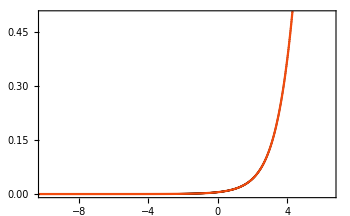
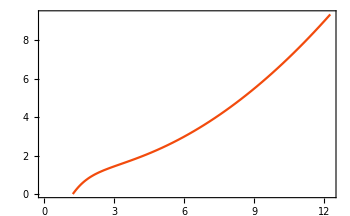

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->{{-10,imax*Δrstar},{-0,0.5}},ImageSize->350,Frame->True], Show[{VrPlot(*,Psirplot*)},ImageSize->350,Frame->True]}]
```

1.2398003637281209688

General::munfl: 0.49 2.061972906550927411948944797749816538010043178669044837084450402073651195984404397914272595667×10^-34593 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.02 1.744309131904679846108196753500606136775716845147591249596390503428007039776308427945394782245×10^-34616 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.49 4.940656458412465441765687928682213723650598026143247644255856825006755072702087518652998363616359924×10^-324 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

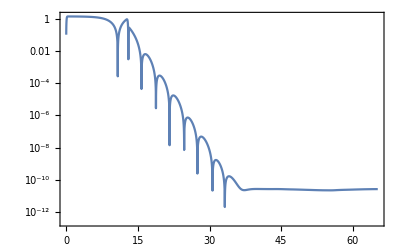

```mathematica
i=0;
(*lambda=5;*)
Offpaclet:ref/Off[General::munfl];
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/m,Evaluate[Abs[ψ[i,j]]]},{j,0,7000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

-Graphics-

```mathematica
data= Table[{(j Δt)/m ,ψ[i,j]},{j,0,7000}]  ;
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
(**)
Print["m = ",m," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 1 , α = 1.22753 , leta = 1 , lambda = 0

File name :

One_way_m1leta1a1.22753l0data.txt

### Final graphs ✓

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
data0=Import["One_way_m1leta1a1.22753l0data.txt","Table"]//ToExpression;
data1=Import["One_way_m1leta1a1.22753l1data.txt","Table"]//ToExpression;
data2=Import["One_way_m1leta1a1.22753l2data.txt","Table"]//ToExpression;
```

Below command : to read the number of lines a txt file has

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"One_way_m1leta1a1.22753l0data.txt","One_way_m1leta1a1.22753l1data.txt","One_way_m1leta1a1.22753l2data.txt"}
```

{7001,10001,7001}

```mathematica
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
```

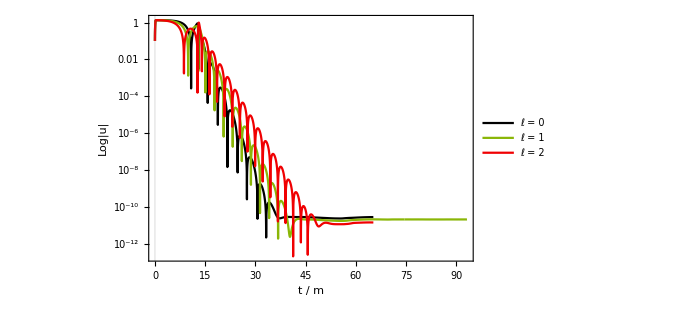

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[;;7000,;;]],data1[[;;10000,;;]],data2[[start;;7000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["ℓ = 0",15],Style["ℓ = 1",15],Style["ℓ = 2",15]},{Scaled[{0.05,0.05}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{5,63},{-0,-30}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
plotlam[1,1,{0,1,2},.15,.7];
```

Horizon = 1.22753

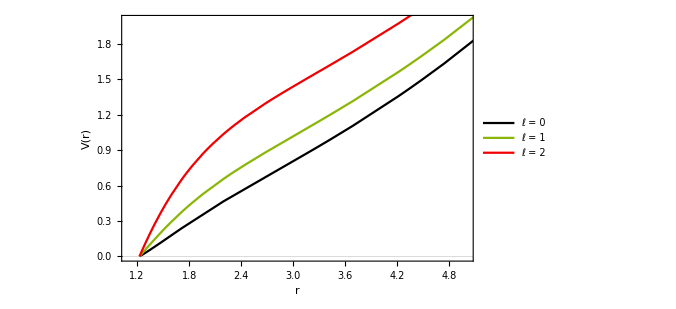

```mathematica
Show[VstarPlot, PlotRange->{{1.1,5},{0,2}},
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
Block[{ε=1,leta},
times=100;
V1=Plot[{Veff[r,2]/.leta->5},{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 5",15]},{0.798,0.7}]},PlotStyle->colorlist[[1]],Frame->True];
V2=Plot[{Veff[r,2]/.leta->10 },{r,-times,times},PlotRange->All,PlotTheme->"Scientific",PlotLegends->{Placed[{Style["ℓ_η = 10",15]},{0.8,0.62}]},PlotStyle->colorlist[[2]],Frame->True];
]
```

```mathematica
Show[{V1,V2},PlotRange->{{-90,90},All},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\Grav_Petrurbations_NMDC\\3rd Run-Plots\\"];
Export["GP_Rin_leta01manymasses.pdf",NotebookRead[PreviousCell[]]]
```

GP_Rin_leta01manymasses.pdf

## Setup - leta = 1 , m = 2

### lambda = 0,1,2

```mathematica
Clear[ψ]
```

```mathematica
FDrin[-10,xstarmax-10^-7,500,50,2]
```

Clear::wrsym: Symbol Null is Protected.

leta = 1, m = 2., lambda = 2

r_horizon = 1.91751

Location of Gaussian's center = 1.9366865485505961874679314860259182751178741455078125

# of Iterations in space = 500

(r_*)^max =  5.09344764009744328503186570845532212819151932898275019747398066307028540261746682730291882279736265  , r^max =  5.9999999999999935107×10^7

(r_*)^min =  -10  ,  r^min =  1.9175115309579704562

I_max = 168

I_min = -331

Space Discretization step = 0.0301869

t_final/M = 25.

# of Iterations in time = J_max = 2366

Time Discretization step = 0.0211308

Δt/(Δr_*) = 0.7

```mathematica
Clear[Viplot,OrigV,VrPlot]
Viplot = ListPlot[Table[{i Δrstar,V[i]},{i,imin,imax}],PlotStyle->Directive[Black,Thick],PlotRange->All];
OrigV = Plot[Veff[x[rstar],lambda],{rstar,imin*Δrstar,(imax-10)*Δrstar},PlotStyle->colorlist,PlotRange->All];
VrPlot=Plot[{Veff[r,2]},{r,horizonsol[leta,m],10*horizonsol[leta,m]},PlotRange->Automatic,PlotStyle->colorlist(*{{horizon,10*horizon},{0,100}}*),AxesOrigin->{0,0},PlotLegends->"Expressions"];
```

```mathematica
(*Psiplot = Plot[PsiSquare[x[rstar]],{rstar,imin*Δrstar,imax*Δrstar},PlotStyle->colorlist[[2]],PlotRange->All];
Psirplot = Plot[PsiSquare[r],{r,horizonsol[leta,a],10*horizonsol[leta,a]},PlotStyle->colorlist[[2]],PlotRange->All];*)
```

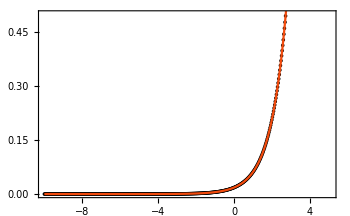
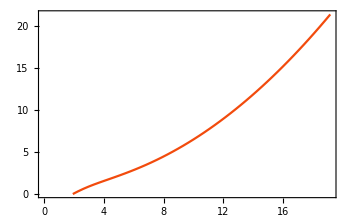

```mathematica
Row[{Show[{Viplot,OrigV},PlotRange->{{-10,imax*Δrstar},{-0,0.5}},ImageSize->350,Frame->True], Show[{VrPlot(*,Psirplot*)},ImageSize->350,Frame->True]}]
```

1.9366865485505961875

General::munfl: 0.49 1.2268510549279476822888218100524876533107822437158678074956447750245134667938738950674493638×10^-177970 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.02 2.41825273756166998316442105178247690419613201720732512764830053763326186054368151681164845296×10^-178089 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.49 2.509853480873532444416969467770564571614503797280769803281975267103431576932660459475723168717110841×10^-321 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

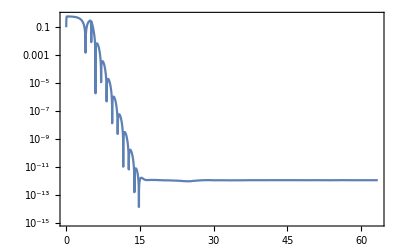

```mathematica
i=0;
Offpaclet:ref/Off[General::munfl];
(*lambda=5;*)
NumberForm[x[i*Δrstar],20]
Block[{$RecursionLimit=Infinity},ListLogPlot[{Table[{(j Δt)/m,Evaluate[Abs[ψ[i,j]]]},{j,0,6000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->All,Frame->True] ]
```

```mathematica
Block[{$RecursionLimit=Infinity},ListPlot[{Table[{(j Δt)/m,Evaluate[ψ[i,j]]},{j,0,3000}]  
(*,Table[{(j Δt)/M,Evaluate[10^3(j Δt)^(-(5))]},{j,1700,jmax}]*)},Joined->True,PlotRange->{{20,100},{-0.01,0.01}}] ]
```

-Graphics-

```mathematica
data= Table[{(j Δt)/m ,ψ[i,j]},{j,0,6000}]  ;
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
(**)
Print["m = ",m," , α = ",a," , leta = ",leta," , lambda = ",lambda];
Export["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt",data,"Table","FieldSeparators"->" "];
(**)
Print["File name :"]
Print["One_way_"<>"m"<>ToString[m]<>"leta"<>ToString[leta]<>"a"<>ToString[a]<>"l"<>ToString[lambda]<>"data.txt"]
```

m = 2 , α = 1.91751 , leta = 1 , lambda = 2

File name :

One_way_m2leta1a1.91751l2data.txt

### Final graphs ✓

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
data0=Import["One_way_m2leta1a1.91751l0data.txt","Table"]//ToExpression;
data1=Import["One_way_m2leta1a1.91751l1data.txt","Table"]//ToExpression;
data2=Import["One_way_m2leta1a1.91751l2data.txt","Table"]//ToExpression;
```

Below command : to read the number of lines a txt file has

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@{"One_way_m2leta1a1.91751l0data.txt","One_way_m2leta1a1.91751l1data.txt","One_way_m2leta1a1.91751l2data.txt"}
```

{6001,6001,6001}

```mathematica
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
```

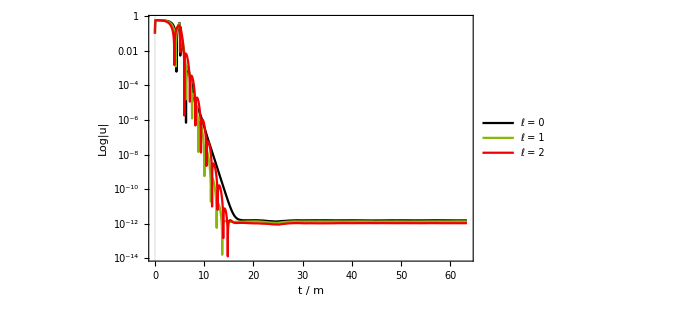

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[;;6000,;;]],data1[[;;6000,;;]],data2[[start;;6000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["ℓ = 0",15],Style["ℓ = 1",15],Style["ℓ = 2",15]},{Scaled[{0.05,0.05}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{2,20},{-0,-33}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
plotlam[1,2,{0,1,2},.15,.7];
```

Horizon = 1.91751

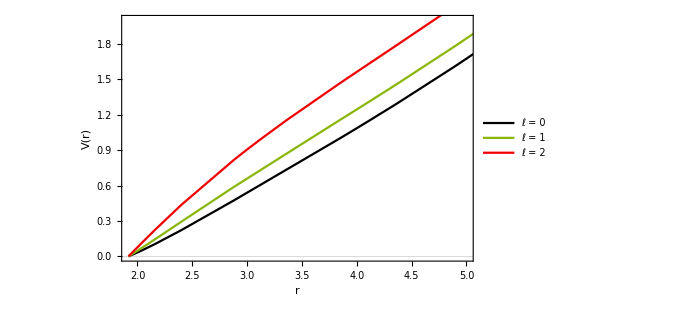

```mathematica
Show[VstarPlot, PlotRange->{{a,5},{0,2}},
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

## Graphs - leta = 1, m = 0.1,0.12,0.13,0.25, 0.6,1,2???

```mathematica
SetDirectory["C:\\Users\\tsits\\OneDrive\\Έγγραφα\\Wolfram Mathematica\\PhD-2\\BhWhTransition\\One_way_data\\"];
dataminus1 = Import["One_way_m0.06leta1a0.0848519l2data.txt","Table"]//ToExpression;
data0=Import["One_way_m0.1leta1a0.14141l2data.txt","Table"]//ToExpression;data1=Import["One_way_m0.12leta1a0.11232l2data.txt","Table"]//ToExpression;data2=Import["One_way_m0.13leta1a0.183808l2data.txt","Table"]//ToExpression;
data3=Import["One_way_m0.25leta1a0.352625l2data.txt","Table"]//ToExpression;
data6 = Import["One_way_m0.6leta1a0.811385l2data.txt","Table"]//ToExpression;
data4=Import["One_way_m1leta1a1.22753l2data.txt","Table"]//ToExpression;
data5=Import["One_way_m2leta1a1.91751l2data.txt","Table"]//ToExpression;
```

```mathematica
null[_String]:=Null
Length@ReadList[#,null@String,NullRecords->True]&/@
{
"One_way_m0.1leta1a0.14141l2data.txt",
"One_way_m0.12leta1a0.11232l2data.txt",
"One_way_m0.13leta1a0.183808l2data.txt",
"One_way_m0.25leta1a0.352625l2data.txt",
"One_way_m0.6leta1a0.811385l2data.txt",
"One_way_m1leta1a1.22753l2data.txt",
"One_way_m2leta1a1.91751l2data.txt"
}
```

{4001,4001,4001,4001,9001,7001,6001}

```mathematica
dataminus1[[;;,2]]=Abs[dataminus1[[;;,2]]];
data0[[;;,2]]=Abs[data0[[;;,2]]];
data1[[;;,2]]=Abs[data1[[;;,2]]];
data2[[;;,2]]=Abs[data2[[;;,2]]];
data3[[;;,2]]=Abs[data3[[;;,2]]];
data6[[;;,2]]=Abs[data6[[;;,2]]];
data4[[;;,2]]=Abs[data4[[;;,2]]];
data5[[;;,2]]=Abs[data5[[;;,2]]];
```

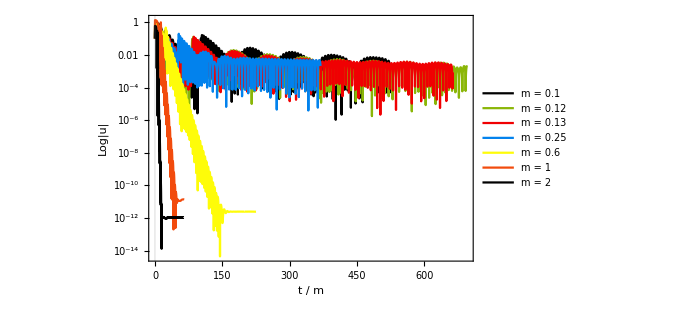

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[start;;4000,;;]],data1[[start;;4000,;;]],data2[[start;;4000,;;]],data3[[start;;4000,;;]],data6[[start;;9000,;;]],data4[[start;;7000,;;]],data5[[start;;6000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["m = 0.1",15],Style["m = 0.12",15],Style["m = 0.13",15],Style["m = 0.25",15],Style["m = 0.6",15],Style["m = 1",15],Style["m = 2",15]},Right(*{Scaled[{0.78,0.15}], {0,0}}*)],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,350},{2,-30}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

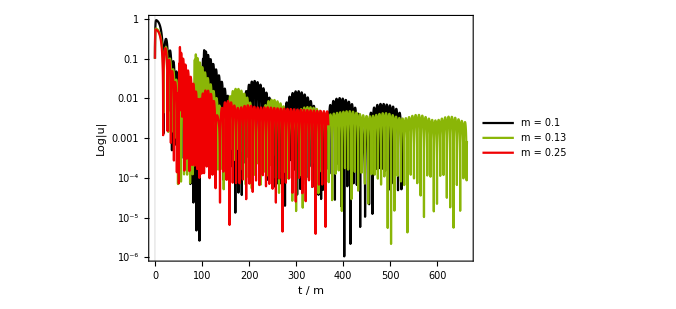

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[start;;4000,;;]],data2[[start;;4000,;;]],data3[[start;;4000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["m = 0.1",15],Style["m = 0.13",15],Style["m = 0.25",15]},{Scaled[{0.03,0.05}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,300},{-0.7,-16}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

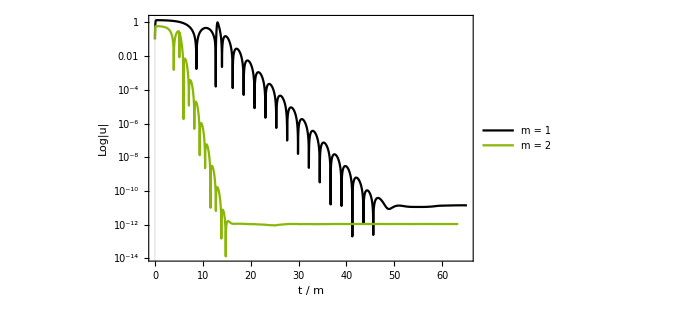

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data4[[start;;7000,;;]],data5[[start;;6000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["m = 1",15],Style["m = 2",15]},{Scaled[{0.78,0.45}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{0,60},{2,-33}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
plotmass[1,{1,2},0.8,0.35]
```

Set::shape: Lists {a1,a2,a3} and {1.22753,1.91751} are not the same shape.

Part::partw: Part 3 of {1,2} does not exist.

Part::partw: Part 3 of {1.22753,1.91751} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {1.22753,1.91751}⟦3⟧ in {r,{1.22753,1.91751}⟦3⟧,200} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

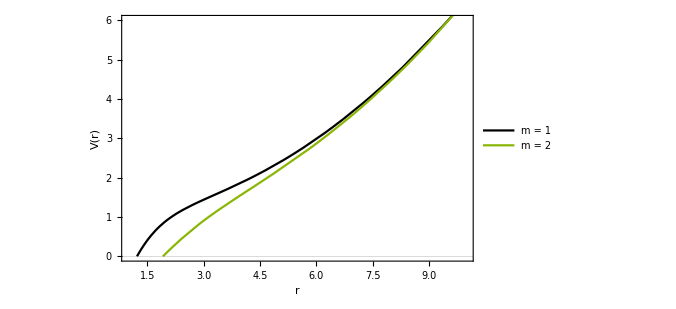

```mathematica
Show[{V1,V2},PlotRange->{{1,10},{0,6}},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```

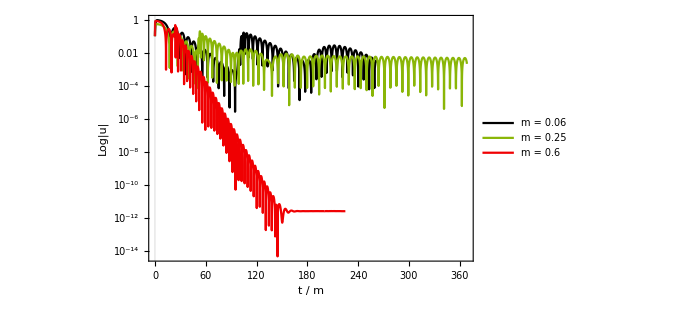

```mathematica
Block[{$RecursionLimit=Infinity,start=1},Show[ListLogPlot[{data0[[start;;2000,;;]],data3[[start;;4000,;;]],data6[[start;;9000,;;]]
},Joined->True,PlotRange->All,Frame->True,ImageSize->500,Background->White,PlotTheme->"Scientific",PlotLegends->Placed[{Style["m = 0.06",15],Style["m = 0.25",15],Style["m = 0.6",15]},{Scaled[{0.03,0.05}], {0,0}}],PlotStyle->colorlist],FrameLabel-> {{RawBoxes[RowBox[{"Log|u|"}]],None},{"t / m",None}},
FrameStyle->Directive[Black,17],
PlotLabel->None,PlotRange->{{10,220},{2,-30}},
LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15}]]
```

```mathematica
Clear[leta,m,a]
plotmass[1,{0.1,0.25,0.6},0.85,0.3]
```

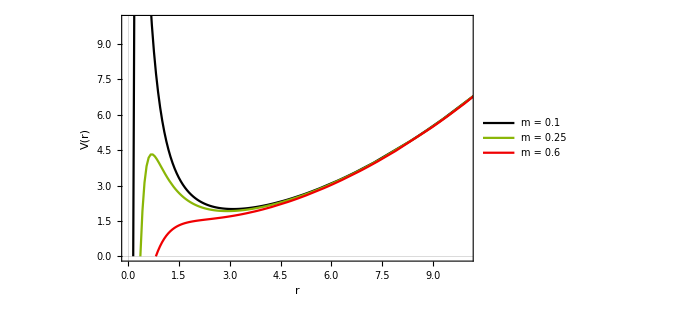

```mathematica
Show[{V1,V2,V3},PlotRange->{{0,10},{0,10}},ImageSize->500,
FrameLabel->{{HoldForm["V(r)" ],None},{HoldForm["r"],None}},
FrameStyle->Directive[Black,17],LabelStyle->{GrayLevel[0],FontFamily->"Times New Roman",FontSize->15},Background->White]
```